```mathematica
(*Quit*)
Clear["Global`*"]
```

## Load Packages

```mathematica
$CKM=True;
$LoadAddOns={"FeynArts"};
Get["FeynCalc`"]
$FAVerbose=0;
Needs["MaTeX`"]
SetOptions[MaTeX,FontSize->16,"Preamble"->Join[{"\\usepackage{amsmath,amssymb,slashed}","\\usepackage{xcolor,txfonts}"}]];
<<FixPolygons`
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

## Constants

From the paper (link), we have the b-tagging rates of:

```mathematica
ϵc=0.1;
ϵu=0.01;
ϵd=0.01;
ϵs=0.01;(*Probability of mistagging other quarks as a "b" - cross section of the background q q̄ production will be multiplied by these.*)

ϵb=0.7;(*Probability of identifying a b quark accurately.*)

bsMisTag=ϵb*(1-ϵs);(*Probability of mis-tagging a sb final state - must tag the b, and not mis-tag the s as a b.*)
BBbarFactor=2;(*This will be multiplied into everything except the cross section for the q q̄ background, since we are considering the production of both B and B̄.*)

systematicUncertainty=0.02;(*2% systematic uncertainty.*)

(*Constants below should be fairly obvious - they're all just couplings in the SM.*)
ℏc=√(0.38937966*10^12(*GeV^2 fb*))(*From https://pdg.lbl.gov/1998/consrpp.pdf*);
αs=0.0761521;(*Running from Z pole with 6 flavors*)
(*All below from https://pdg.lbl.gov/2020/reviews/rpp2020-rev-phys-constants.pdf*)
Zmass=91.1876;
Wmass=80.379;
alpha=1/133.;
αEM=1/128;
mb=4.2;
mt=163.579;(*From RunDec file - MSbar mass - is this PDG?*)
eCharge=√(4π αEM);
gCharge=√(4π αs);
sinθWSq=0.23121;
θW=ArcSin[√sinθWSq];
cosθWSq=1-sinθWSq;
θZμLb=eCharge((Tan[θW]-Cot[θW])/2);
θZμRb=eCharge Tan[θW];
θZqLUpTypeb=-eCharge((Tan[θW]-3Cot[θW])/6);
θZqRUpTypeb=-eCharge((4Tan[θW])/6);
θZqLDownTypeb=-eCharge((Tan[θW]+3Cot[θW])/6);
θZqRDownTypeb=eCharge((2Tan[θW])/6);
```

From the paper (link), we draw some preliminary values of the relevant Wilson coefficients, to use as a benchmark. Further, the various necessary couplings and constants may be drawn from PDG.

```mathematica
(*C9blow=-0.35;
C10blow=-C9blow;


Cp9blow=-0.32;
Cp10blow=0.06;
CSblow=-0.004;
CPblow=-CSblow;
CpSblow=-0.004;
CpPblow=CpSblow;*)

(*Updated benchmarks post LFUV status update Dec 2022*)
C9blow=-0.81;
C10blow=0.12;
C9upper2σblow=-1.25;
C10upper2σblow=0.32;
C9upper1σblow=-1.03;
C10upper1σblow=0.21;
C9lower1σblow=-0.59;
C10lower1σblow=0.05;
C9lower2σblow=-0.36;
C10lower2σblow=0.00;

Cp9blow=0;
Cp10blow=0;
CSblow=0;
CPblow=-CSblow;
CpSblow=0;
CpPblow=CpSblow;

(*We follow a slightly different convention for the scalar operators, not including the Subscript[m, b] factor in their normalisation. Since we divide the operators in the paper by Subscript[m, b], we must mutliply their coefficient (benchmarks) by an identical factor.*)
CSblow=CSblow*mb;
CPblow=CPblow*mb;
CpSblow=CpSblow*mb;
CpPblow=CpPblow*mb;


GFermi=1.1663787*10^-5;(*https://pdg.lbl.gov/2021/reviews/rpp2020-rev-phys-constants.pdf*)
higgsVEV=1/(√(√2GFermi));
Vtb=1.013;(*https://pdg.lbl.gov/2020/reviews/rpp2020-rev-ckm-matrix.pdf*)
Vts=38.8*10^-3;(*https://pdg.lbl.gov/2020/reviews/rpp2020-rev-ckm-matrix.pdf*)
αEM=1/128;(*Running from Z pole with 6 flavors*)
mb=4.2;
Nc=3(*colours*);
invGeV2TOpb=ℏc^2/10^3;(*Conversion factor for inverse squared GeV to picobarns.*)

coefficientNormalisation=4(GFermi/(√2))Vtb Vts;
cN=(alpha/(4π))coefficientNormalisation;(*Wilson operator normalizations.*)
```

```mathematica
coefficientNormalisation=4(GFermi/(√2))Vtb Vts;
cN=(alpha/(4π))coefficientNormalisation;
```

```mathematica
defaultScale=10^4;
defaultLumi=10^6(*/pb*);(*1/ab*)
TeV=1000;
minC9=-1.5;
maxC9=1.5;
minC10=-1.5;
maxC10=1.5;
```

## Polarizers

```mathematica
PRight=GA[6];
PLeft=GA[7];

polP=((√(1-Pp))/(√2))PLeft+((√(1+Pp))/(√2))PRight//DiracSimplify;
polM=((√(1-Pm))/(√2))PLeft+((√(1+Pm))/(√2))PRight//DiracSimplify;
```

Eventually, P_- = -P_+,  P_- > 0 will be taken. Verified for the White Paper.

## NP Signal

### Matrix Element

```mathematica
(*Anti-muon Momentum: pmup, Muon momumtum: pmum, b quark momentum: pb, s quark momentum: psbar.*)
(*Vector Matrix Elements*)
M9=EFTNormalization*c9*Contract[(SpinorVBar[pmup].polP.GA[α9].polM.SpinorU[pmum])*(SpinorUBar[pb].GA[α9].PLeft.SpinorV[psbar])];
M10=EFTNormalization*c10*Contract[(SpinorVBar[pmup].polP.GA[α10].GA5.polM.SpinorU[pmum])*(SpinorUBar[pb].GA[α10].PLeft.SpinorV[psbar])];
Mp9=EFTNormalization*cp9*Contract[(SpinorVBar[pmup].polP.GA[β9].polM.SpinorU[pmum])*(SpinorUBar[pb].GA[β9].PRight.SpinorV[psbar])];
Mp10=EFTNormalization*cp10*Contract[(SpinorVBar[pmup].polP.GA[β10].GA5.polM.SpinorU[pmum])*(SpinorUBar[pb].GA[β10].PRight.SpinorV[psbar])];

(*Scalar Matrix Elements*)
MS=EFTNormalization*cS*Contract[(SpinorVBar[pmup].polP.polM.SpinorU[pmum])*(SpinorUBar[pb].PRight.SpinorV[psbar])];
MP=EFTNormalization*cP*Contract[(SpinorVBar[pmup].polP.GA5.polM.SpinorU[pmum])*(SpinorUBar[pb].PRight.SpinorV[psbar])];
MpS=EFTNormalization*cpS*Contract[(SpinorVBar[pmup].polP.polM.SpinorU[pmum])*(SpinorUBar[pb].PLeft.SpinorV[psbar])];
MpP=EFTNormalization*cpP*Contract[(SpinorVBar[pmup].polP.GA5.polM.SpinorU[pmum])*(SpinorUBar[pb].PLeft.SpinorV[psbar])];

M=M9+M10+Mp10+Mp9+MS+MP+MpS+MpP//Simplify;
Mbar=ComplexConjugate[M,Conjugate->{c9,c10,cp9,cp10,cS,cP,cpS,cpP,EFTNormalization}];
Msq=Nc*DiracSimplify[FermionSpinSum[M*ComplexConjugate[M,Conjugate->{c9,c10,cp9,cp10,cS,cP,cpS,cpP,EFTNormalization}],ExtraFactor->1]]//Simplify;
```

```mathematica
Msq/.{cp9->0,cp10->0,cS->0,cpS->0,cP->0,cpP->0}//Simplify
```

-12 EFTNormalization Conjugate[EFTNormalization] (Conjugate[c9] ((Pm+1) (Pp-1) (c10+c9) (OverBar[pb]·OverBar[pmum]) (OverBar[pmup]·OverBar[psbar])-(Pm-1) (Pp+1) (c10-c9) (OverBar[pb]·OverBar[pmup]) (OverBar[pmum]·OverBar[psbar]))+Conjugate[c10] ((Pm-1) (Pp+1) (c10-c9) (OverBar[pb]·OverBar[pmup]) (OverBar[pmum]·OverBar[psbar])+(Pm+1) (Pp-1) (c10+c9) (OverBar[pb]·OverBar[pmum]) (OverBar[pmup]·OverBar[psbar])))

### Kinematic Definitions for μ^+ μ^- → b s̄ (Verified)

```mathematica
(*  pp:  momentum of incoming mu+ *)
(*  pm:  momentum of incoming mu- *)
(*  pb:  momentum of outgoing b *)
(*  ps:  momentum of outgoing s-bar *)

(* all particles massless *)
(*ScalarProduct[pp,pp]=ScalarProduct[pm,pm]=0;
ScalarProduct[pb,pb]=ScalarProduct[ps,ps]=0;
 
ScalarProduct[pp,pm]=ScalarProduct[pb,ps]=s/2;
ScalarProduct[pp,pb]=ScalarProduct[pm,ps]=s/4*(1+Cos[θ]);
ScalarProduct[pp,ps]=ScalarProduct[pm,pb]=s/4*(1-Cos[θ]);
*)
(* all particles massless *)
ScalarProduct[pmup,pmup]=ScalarProduct[pmum,pmum]=0;
ScalarProduct[pb,pb]=ScalarProduct[psbar,psbar]=0;
 
ScalarProduct[pmup,pmum]=ScalarProduct[pb,psbar]=s/2;
ScalarProduct[pmup,pb]=ScalarProduct[pmum,psbar]=s/4*(1+Cos[θ]);
ScalarProduct[pmup,psbar]=ScalarProduct[pmum,pb]=s/4*(1-Cos[θ]);
```

### Differential Cross Section

#### 1, cos(θ), cos(2θ) basis

```mathematica
(*Decomposing the differential Cross section into coefficients of 1, Cos(θ), Cos(2θ).*)
dσdΩ=Msq*(1/(2s))(1/(32 π^2))//TrigReduce//FullSimplify;
part2θ=Coefficient[dσdΩ,Cos[2θ]]//Simplify;
partθ=Coefficient[dσdΩ,Cos[θ]]//Simplify;
part1=(dσdΩ-(partθ Cos[θ]+part2θ Cos[2θ]))//Simplify;
```

```mathematica
(*Decompose into scalar and vector contributions, which further decompose into LH and RH quark final states. These decompositions are all related by various signs - we will find a general function to express it.*)
part1vec=part1/.{cS->0,cP->0,cpS->0,cpP->0}//FullSimplify;
part1Lvec=part1vec/.{cp9->0,cp10->0}//FullSimplify;
part1Rvec=part1vec/.{c9->0,c10->0}//FullSimplify;
(part1Rvec/.{cp9->a,cp10->b}//FullSimplify)==(part1Lvec/.{c9->a,c10->b}//FullSimplify)//Simplify
part1Rvec/.{cp9->a,cp10->b}//FullSimplify

part1scl=part1-part1vec//FullSimplify;
part1Rscl=part1scl/.{cpS->0,cpP->0}//FullSimplify;
part1Lscl=part1scl-part1Rscl//FullSimplify;
(part1Rscl/.{cS->a,cP->b}//FullSimplify)==
(part1Lscl/.{cpS->a,cpP->b}//FullSimplify)//Simplify
(part1Rscl/.{cS->a,cP->b}//FullSimplify)
```

True

-(9 EFTNormalization s Conjugate[EFTNormalization] (Conjugate[a] (a (Pm Pp-1)+b (Pp-Pm))+Conjugate[b] (a (Pp-Pm)+b (Pm Pp-1))))/(256 π^2)

True

(3 EFTNormalization s Conjugate[EFTNormalization] (Conjugate[a] (a Pm Pp+a+b (Pm+Pp))+Conjugate[b] (a (Pm+Pp)+b Pm Pp+b)))/(128 π^2)

```mathematica
(*Mathematica doesn't allow me to define (A^1)_±, so I just used 1,2 to denote those.*)
A1func[n_?IntegerQ][a_,b_]=((EFTNormalization*Conjugate[EFTNormalization] Nc s)/(256 π^2)) ((a*Conjugate[a]+b*Conjugate[b])(1+(-1)^n Pp Pm)+2Re[a*Conjugate[b]](Pm+(-1)^n Pp));
part1-3(A1func[1][c9,c10]+A1func[1][cp9,cp10])-2(A1func[2][cS,cP]+A1func[2][cpS,cpP])//FullSimplify
```

0

```mathematica
(*Similar story here, just for the vector coefficients.*)
partθLvec=partθ/.{cp9->0,cp10->0}//FullSimplify;
partθRvec=partθ/.{c9->0,c10->0}//FullSimplify;
(partθLvec/.{c9->a,c10->b}//FullSimplify)+(partθRvec/.{cp9->a,cp10->b}//FullSimplify)==0//Simplify
(partθLvec/.{c9->a,c10->b}//FullSimplify)
```

True

(3 EFTNormalization s Conjugate[EFTNormalization] (Conjugate[a] (a (Pp-Pm)+b (Pm Pp-1))+Conjugate[b] (a (Pm Pp-1)+b (Pp-Pm))))/(64 π^2)

```mathematica
Aθfunc[a_,b_]=((EFTNormalization*Conjugate[EFTNormalization] Nc s)/(256 π^2))((a*Conjugate[a]+b*Conjugate[b])(Pm-Pp)+2Re[a*Conjugate[b]](1-Pm Pp));
partθ-4(Aθfunc[cp9,cp10]-Aθfunc[c9,c10])//FullSimplify
```

0

```mathematica
(*This is an even function, so we can reuse the A1func again.*)
part2θLvec=part2θ/.{cp9->0,cp10->0}//FullSimplify;
part2θRvec=part2θ/.{c9->0,c10->0}//FullSimplify;
(part2θLvec/.{c9->a,c10->b}//FullSimplify)==(part2θRvec/.{cp9->a,cp10->b}//FullSimplify)//Simplify
(part2θLvec/.{c9->a,c10->b}//FullSimplify)
```

True

-(3 EFTNormalization s Conjugate[EFTNormalization] (Conjugate[a] (a (Pm Pp-1)+b (Pp-Pm))+Conjugate[b] (a (Pp-Pm)+b (Pm Pp-1))))/(256 π^2)

```mathematica
part2θ-(A1func[1][c9,c10]+A1func[1][cp9,cp10])//FullSimplify
```

0

#### 1, cos(θ), cos^2(θ) basis

```mathematica
(*Decomposing the differential Cross section into coefficients of 1, Cos(θ), Cos(2θ).*)
Clear[dσdΩ,partθ2,partθ,part1]
dσdΩ=(Msq*(1/(2s))(1/(32 π^2))//TrigExpand)/.{Sin[θ]^2->1-Cos[θ]^2};
partθ2=Coefficient[dσdΩ,Cos[θ]^2]//Simplify;
partθ=Coefficient[dσdΩ,Cos[θ]]//Simplify;
part1=(dσdΩ-(partθ*Cos[θ]+partθ2*Cos[θ]^2))//Simplify;
dσdΩ==part1+partθ Cos[θ]+partθ2 Cos[θ]^2//Simplify
```

True

```mathematica
(*Decompose into scalar and vector contributions, which further decompose into LH and RH quark final states. These decompositions are all related by various signs - we will find a general function to express it.*)
part1vec=part1/.{cS->0,cP->0,cpS->0,cpP->0}//FullSimplify;
part1Lvec=part1vec/.{cp9->0,cp10->0}//FullSimplify;
part1Rvec=part1vec/.{c9->0,c10->0}//FullSimplify;
(part1Rvec/.{cp9->a,cp10->b}//FullSimplify)==(part1Lvec/.{c9->a,c10->b}//FullSimplify)//Simplify
part1Rvec/.{cp9->a,cp10->b}//FullSimplify

part1scl=part1-part1vec//FullSimplify;
part1Rscl=part1scl/.{cpS->0,cpP->0}//FullSimplify;
part1Lscl=part1scl-part1Rscl//FullSimplify;
(part1Rscl/.{cS->a,cP->b}//FullSimplify)==
(part1Lscl/.{cpS->a,cpP->b}//FullSimplify)//Simplify
(part1Rscl/.{cS->a,cP->b}//FullSimplify)
```

True

-(3 EFTNormalization s Conjugate[EFTNormalization] (Conjugate[a] (a (Pm Pp-1)+b (Pp-Pm))+Conjugate[b] (a (Pp-Pm)+b (Pm Pp-1))))/(128 π^2)

True

(3 EFTNormalization s Conjugate[EFTNormalization] (Conjugate[a] (a Pm Pp+a+b (Pm+Pp))+Conjugate[b] (a (Pm+Pp)+b Pm Pp+b)))/(128 π^2)

```mathematica
(*We can reuse A1func here, with mildly different coefficients on the vector aspect.*)
part1-2(A1func[1][c9,c10]+A1func[1][cp9,cp10])-2(A1func[2][cS,cP]+A1func[2][cpS,cpP])//FullSimplify
```

0

```mathematica
(*Similar story here, just for the vector coefficients.*)
partθLvec=partθ/.{cp9->0,cp10->0}//FullSimplify;
partθRvec=partθ/.{c9->0,c10->0}//FullSimplify;
(partθLvec/.{c9->a,c10->b}//FullSimplify)+(partθRvec/.{cp9->a,cp10->b}//FullSimplify)==0//Simplify
(partθLvec/.{c9->a,c10->b}//FullSimplify)
```

True

(3 EFTNormalization s Conjugate[EFTNormalization] (Conjugate[a] (a (Pp-Pm)+b (Pm Pp-1))+Conjugate[b] (a (Pm Pp-1)+b (Pp-Pm))))/(64 π^2)

```mathematica
(*As expected, this should be unchanged. The only difference is shifting between (1,cos(2θ) = 2 cos^2(θ)-1) and (1, cos(θ)^2)*)
partθ-(Aθfunc[cp9,cp10]-Aθfunc[c9,c10])//FullSimplify
```

1/(256 π^2)9 EFTNormalization s Conjugate[EFTNormalization] (Conjugate[c10] (c10 (Pp-Pm)+c9 (Pm Pp-1))+Conjugate[c9] (c10 Pm Pp-c10-c9 Pm+c9 Pp)+Conjugate[cp10] (-Pp (cp10+cp9 Pm)+cp10 Pm+cp9)+Conjugate[cp9] (-Pp (cp10 Pm+cp9)+cp10+cp9 Pm))

```mathematica
(*This is an even function, so we can reuse the A1func again.*)
partθ2Lvec=partθ2/.{cp9->0,cp10->0}//FullSimplify;
partθ2Rvec=partθ2/.{c9->0,c10->0}//FullSimplify;
(partθ2Lvec/.{c9->a,c10->b}//FullSimplify)==(partθ2Rvec/.{cp9->a,cp10->b}//FullSimplify)//Simplify
(partθ2Lvec/.{c9->a,c10->b}//FullSimplify)
```

True

-(3 EFTNormalization s Conjugate[EFTNormalization] (Conjugate[a] (a (Pm Pp-1)+b (Pp-Pm))+Conjugate[b] (a (Pp-Pm)+b (Pm Pp-1))))/(128 π^2)

```mathematica
partθ2-2(A1func[1][c9,c10]+A1func[1][cp9,cp10])//FullSimplify
```

0

### Cross Section

```mathematica
σNPF[eCM_:defaultScale,Pp_:0,Pm_:0,c9_:C9bench,c10_: C10bench,cp9_:0,cp10_:0,cS_:0,cP_:0,cpS_:0,cpP_:0]=((invGeV2TOpb*bsMisTag)/(2 eCM^2))(1/(32 π^2))Integrate[Msq*Sin[θ]/.{s->eCM^2},{θ,π/2,π},{ϕ,0,2π}]/.{EFTNormalization->cN}//FullSimplify;
σNPB[eCM_:defaultScale,Pp_:0,Pm_:0,c9_:C9bench,c10_: C10bench,cp9_:0,cp10_:0,cS_:0,cP_:0,cpS_:0,cpP_:0]=((invGeV2TOpb*bsMisTag)/(2 eCM^2))(1/(32 π^2))Integrate[Msq*Sin[θ]/.{s->eCM^2},{θ,0,π/2},{ϕ,0,2π}]/.{EFTNormalization->cN}//FullSimplify;
σNP[eCM_:defaultScale,Pp_:0,Pm_:0,c9_:C9bench,c10_: C10bench,cp9_:0,cp10_:0,cS_:0,cP_:0,cpS_:0,cpP_:0]=((invGeV2TOpb*bsMisTag)/(2 eCM^2))(1/(32 π^2))Integrate[Msq*Sin[θ]/.{s->eCM^2},{θ,0,π},{ϕ,0,2π}]/.{EFTNormalization->cN}//FullSimplify
```

1.6156×10^-12 eCM^2 (4 Conjugate[c10] (-Pp (c10 Pm+c9)+c10+c9 Pm)+4 Conjugate[c9] (-Pp (c10+c9 Pm)+c10 Pm+c9)+3 Conjugate[cP] (cP Pm Pp+cP+cS (Pm+Pp))+3 cP Pm Conjugate[cS]+3 cP Pp Conjugate[cS]+4 Conjugate[cp10] (-Pp (cp10 Pm+cp9)+cp10+cp9 Pm)+4 cp10 Pm Conjugate[cp9]-4 cp10 Pp Conjugate[cp9]-4 cp9 Pm Pp Conjugate[cp9]+4 cp9 Conjugate[cp9]+3 cpS Pm Conjugate[cpP]+3 cpP Pm Conjugate[cpS]+3 cpS Pp Conjugate[cpP]+3 cpP Pp Conjugate[cpS]+3 cpP Pm Pp Conjugate[cpP]+3 cpP Conjugate[cpP]+3 cpS Pm Pp Conjugate[cpS]+3 cpS Conjugate[cpS]+3 cS Pm Pp Conjugate[cS]+3 cS Conjugate[cS])

### AFB

```mathematica
AFBNP[eCM_:defaultScale,Pp_:0,Pm_:0,c9_:C9bench,c10_: C10bench,cp9_:0,cp10_:0,cS_:0,cP_:0,cpP_:0]=(σNPF[eCM,Pp,Pm,c9,c10]-σNPB[eCM,Pp,Pm,c9,c10])/σNP[eCM,Pp,Pm,c9,c10];
AFBNP[]
```

(6189.63 (0.0000807802 ((4 C10bench+3 C9bench) Conjugate[C10bench]+(3 C10bench+4 C9bench) Conjugate[C9bench])-0.0000807802 ((4 C10bench-3 C9bench) Conjugate[C10bench]+(4 C9bench-3 C10bench) Conjugate[C9bench])))/(4 C10bench Conjugate[C10bench]+4 C9bench Conjugate[C9bench])

```mathematica
AFBNP[10TeV,-0,0]//Simplify
AFBNP[10TeV,-0.5,0.5]//Simplify
```

(0.75 C9bench Conjugate[C10bench]+0.75 C10bench Conjugate[C9bench])/(C10bench Conjugate[C10bench]+C9bench Conjugate[C9bench])

(0.75 C9bench Conjugate[C10bench]+0.75 C10bench Conjugate[C9bench]+0.6 C10bench Conjugate[C10bench]+0.6 C9bench Conjugate[C9bench])/(0.8 C9bench Conjugate[C10bench]+0.8 C10bench Conjugate[C9bench]+1. C10bench Conjugate[C10bench]+1. C9bench Conjugate[C9bench])

```mathematica
AFBNP[10TeV,-0.5,0.5,C9blow,C10blow]//Simplify
```

0.498078

```mathematica
AFBNP[10TeV,Pp,Pm,C9,C10]//Simplify//InputForm
```

((-0.7500000000000001*C10*Pm + 0.7500000000000001*C10*Pp + 
    C9*(-0.7500000000000001 + 0.7500000000000001*Pm*Pp))*Conjugate[C10] + 
  (-0.7500000000000001*C9*Pm + 0.7500000000000001*C9*Pp + 
    C10*(-0.7500000000000001 + 0.7500000000000001*Pm*Pp))*Conjugate[C9])/
 ((C9*(-1.*Pm + Pp) + C10*(-1. + Pm*Pp))*Conjugate[C10] + (C10*(-1.*Pm + Pp) + C9*(-1. + Pm*Pp))*
   Conjugate[C9])

```mathematica
Simplify[AFBNP[10TeV,Pp,Pm,C9,C10],Assumptions->{C9∈Reals,C10∈Reals}]//Rationalize//Simplify
Simplify[AFBNP[10TeV,0,0,C9,C10],Assumptions->{C9∈Reals,C10∈Reals}]//Rationalize//Simplify
```

(-3 C10^2 (Pm-Pp)+6 C10 C9 (Pm Pp-1)+3 C9^2 (Pp-Pm))/(4 (C10^2 (Pm Pp-1)+2 C10 C9 (Pp-Pm)+C9^2 (Pm Pp-1)))

(3 C10 C9)/(2 (C10^2+C9^2))

```mathematica
AFBNP[10TeV,0,0,C9blow,C10blow]
AFBNP[]
```

-0.21745

(6189.63 (0.0000807802 ((4 C10bench+3 C9bench) Conjugate[C10bench]+(3 C10bench+4 C9bench) Conjugate[C9bench])-0.0000807802 ((4 C10bench-3 C9bench) Conjugate[C10bench]+(4 C9bench-3 C10bench) Conjugate[C9bench])))/(4 C10bench Conjugate[C10bench]+4 C9bench Conjugate[C9bench])

```mathematica
C9blow
C10blow
```

-0.81

0.12

```mathematica
C9bench
C10bench
```

C9bench

C10bench

## RG Flow

## High to EW

### Vectors

```mathematica
θrge=(1/3)g2^2;
ηrge=(4/3)g1^2;
thrge=θrge/ηrge;
etarge[a_,b_]:=Symbol["y"<>ToString@a]*Symbol["y"<>ToString@b]
eta[ff_]:=etarge[StringSplit[(ToString@ff),""][[1]],StringSplit[(ToString@ff),""][[2]]]
```

```mathematica
(*This will be organized as an RGE matrix acting on the vector (Subscript[C, lq]^(1), Subscript[C, lq]^(3), Subscript[C, ld], Subscript[C, qe], Subscript[C, ed], Subscript[C, Hq]^(1), Subscript[C, Hq]^(3), Subscript[C, Hd])*)
GaugeSMEFT=ηrge{{2 eta[ll]+9eta[lq],27thrge,0,eta[el],0,eta[hl],0,0},{9thrge,9eta[lq]-16thrge,0,0,0,0,thrge,0},{0,0,2eta[ll]-9eta[ld],0,eta[el],0,0,eta[hl]},{2eta[el],0,0,eta[ee]-9eta[qe],0,eta[eh],0,0},{0,0,2 eta[el],0,eta[ee]+9eta@ed,0,0,eta@eh},{2 eta@hl,0,0,eta@eh,0,eta@hh,0,0},{0,2 thrge,0,0,0,0,-17 thrge,0},{0,0,2eta@lh,0,eta@eh,0,0,2 eta@hh}};

qgam=(1/2)Ytt^2;
hgam=Nc Ytt^2;
tyuk=Ytt^2;
ugam=Ytt^2;

YukawaSMEFT=DiagonalMatrix[{qgam,qgam,0,qgam,0,(3/2)tyuk+qgam+2 hgam,(1/2)tyuk+2hgam+qgam,2hgam}];
YukawaSMEFT[[6,7]]=((-9)/2)tyuk;
YukawaSMEFT[[7,6]]=((-3)/2)tyuk;

vecFlowSMEFT=YukawaSMEFT+GaugeSMEFT;

MatrixForm@GaugeSMEFT
MatrixForm@YukawaSMEFT
```

(4/3 g1^2 (2 yl^2+9 yl yq) | 9 g2^2 | 0 | 4/3 g1^2 ye yl | 0 | 4/3 g1^2 yh yl | 0 | 0
3 g2^2 | 4/3 g1^2 (9 yl yq-(4 g2^2)/g1^2) | 0 | 0 | 0 | 0 | g2^2/3 | 0
0 | 0 | 4/3 g1^2 (2 yl^2-9 yd yl) | 0 | 4/3 g1^2 ye yl | 0 | 0 | 4/3 g1^2 yh yl
8/3 g1^2 ye yl | 0 | 0 | 4/3 g1^2 (ye^2-9 ye yq) | 0 | 4/3 g1^2 ye yh | 0 | 0
0 | 0 | 8/3 g1^2 ye yl | 0 | 4/3 g1^2 (9 yd ye+ye^2) | 0 | 0 | 4/3 g1^2 ye yh
8/3 g1^2 yh yl | 0 | 0 | 4/3 g1^2 ye yh | 0 | (4 g1^2 yh^2)/3 | 0 | 0
0 | (2 g2^2)/3 | 0 | 0 | 0 | 0 | -(17 g2^2)/3 | 0
0 | 0 | 8/3 g1^2 yh yl | 0 | 4/3 g1^2 ye yh | 0 | 0 | (8 g1^2 yh^2)/3)

(Ytt^2/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | Ytt^2/2 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | Ytt^2/2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 8 Ytt^2 | -(9 Ytt^2)/2 | 0
0 | 0 | 0 | 0 | 0 | -(3 Ytt^2)/2 | 7 Ytt^2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 6 Ytt^2)

```mathematica
ye=-1;yl=-1/2;yd=-1/3;yu=2/3;yq=1/6;yh=1/2;Nc=3;
EWcoefficients=(IdentityMatrix@8-(1/(32 π^2))Log[(Λ/μEW)^2]vecFlowSMEFT).Transpose@{{C1lqhigh,C3lqhigh,Cldhigh,Cqehigh,Cedhigh,C1Hqhigh,C3Hqhigh,CHdhigh}}//Simplify;
(*EWcoefficients2=(IdentityMatrix@8-(1/(32 π^2))Log[(Λ/μEW)^2]vecFlowSMEFT).Transpose@{{C1lq,C3lq,Cld,Cqe,Ced,C1Hqhigh,C3Hqhigh,CHdhigh}}//Simplify;*)
{{C1lqEW,C3lqEW,CldEW,CqeEW,CedEW,C1HqEW,C3HqEW,CHdEW}}=Transpose@EWcoefficients;
EWcoefficients//MatrixForm
```

((log(Λ^2/μEW^2) (2 C1Hqhigh g1^2+2 C1lqhigh g1^2-3 C1lqhigh Ytt^2-54 C3lqhigh g2^2-4 Cqehigh g1^2))/(192 π^2)+C1lqhigh
(log(Λ^2/μEW^2) (C3lqhigh (6 g1^2+32 g2^2-3 Ytt^2)-2 g2^2 (9 C1lqhigh+C3Hqhigh)))/(192 π^2)+C3lqhigh
(g1^2 (-2 Cedhigh+CHdhigh+4 Cldhigh) log(Λ^2/μEW^2))/(96 π^2)+Cldhigh
(log(Λ^2/μEW^2) (4 C1Hqhigh g1^2-8 C1lqhigh g1^2-20 Cqehigh g1^2-3 Cqehigh Ytt^2))/(192 π^2)+Cqehigh
(g1^2 (-8 Cedhigh+CHdhigh-2 Cldhigh) log(Λ^2/μEW^2))/(48 π^2)+Cedhigh
(log(Λ^2/μEW^2) (-2 C1Hqhigh (g1^2+24 Ytt^2)+4 C1lqhigh g1^2+27 C3Hqhigh Ytt^2+4 Cqehigh g1^2))/(192 π^2)+C1Hqhigh
(log(Λ^2/μEW^2) (9 C1Hqhigh Ytt^2+34 C3Hqhigh g2^2-42 C3Hqhigh Ytt^2-4 C3lqhigh g2^2))/(192 π^2)+C3Hqhigh
(log(Λ^2/μEW^2) (Cedhigh g1^2-CHdhigh (g1^2+9 Ytt^2)+Cldhigh g1^2))/(48 π^2)+CHdhigh)

```mathematica
(*EWcoefficients2//.{OLP->1,g1^2->e^2/cW2,g2^2->e^2/sW2,Ytt^2->e^2(mt^2/(2 mW^2 sW2)),mZ->√(mW^2/cW2),v^2->4 mW^2(sW2/e^2),gZ->e/(√(cW2 sW2)),C1Hqhigh->0,C3Hqhigh->0,CHdhigh->0}//Simplify//Expand//MatrixForm*)
```

### Scalars

```mathematica
CledqEW=(1-(1/(32 π^2))Log[(Λ/μEW)^2](qgam-(6(yd(yq-ye)+ye(yq+ye))g1^2+3(Nc-1/Nc)g3^2)))Cledqhigh;
CledqconjEW=(1-(1/(32 π^2))Log[(Λ/μEW)^2](-(6(yd(yq-ye)+ye(yq+ye))g1^2+3(Nc-1/Nc)g3^2)))Cledqconjhigh;
```

## EW to Low

### Vectors

```mathematica
(*qe=-1;qd=-1/3;qu=2/3;
Zcc=(g2^2/(2 mW^2))v^2;
CVLLedEW=C1lqEW+C3lqEW-Zcc (sW2 qe+1/2)(C1HqEW+C3HqEW)//Simplify
CVRRedEW=CedEW-Zcc(sW2 qe)CHdEW//Simplify
CVLRedEW=CldEW-Zcc(1/2+sW2 qe)CHdEW//Simplify
CVLRdeEW=CqeEW-Zcc (sW2 qe)(C1HqEW+C3HqEW)//Simplify
Clear[qe,qd,qu]*)
```

```mathematica
Zcc=(gZ^2/(2 mZ^2))v^2;
CVLLedEW=C1lqEW+C3lqEW-Zcc (sW2 qe+1/2)(C1HqEW+C3HqEW);
CVLRdeEW=CqeEW-Zcc (sW2 qe)(C1HqEW+C3HqEW);
CVRRedEW=CedEW-Zcc(sW2 qe)CHdEW;
CVLRedEW=CldEW-Zcc(1/2+sW2 qe)CHdEW;
```

```mathematica
λrge=(4/3)e^2;
lambdarge[a_,b_]:=Symbol["q"<>ToString@a]*Symbol["q"<>ToString@b]
lambda[ff_]:=lambdarge[StringSplit[(ToString@ff),""][[1]],StringSplit[(ToString@ff),""][[2]]]
(*This will be organized as an RGE matrix acting on the vector (Subscript[C, ed]^VLL, Subscript[C, de]^VLR, Subscript[C, ed]^VLR, Subscript[C, ed]^VRR)*)
vecFlowLEFT=λrge{{lambda@ee+9lambda@ed,lambda@ee,0,0},{lambda@ee,lambda@ee-9lambda@ed,0,0},{0,0,lambda@ee-9lambda@ed,lambda@ee},{0,0,lambda@ee,lambda@ee+9lambda@ed}};
vecFlowLEFT//MatrixForm
```

(4/3 e^2 (9 qd qe+qe^2) | (4 e^2 qe^2)/3 | 0 | 0
(4 e^2 qe^2)/3 | 4/3 e^2 (qe^2-9 qd qe) | 0 | 0
0 | 0 | 4/3 e^2 (qe^2-9 qd qe) | (4 e^2 qe^2)/3
0 | 0 | (4 e^2 qe^2)/3 | 4/3 e^2 (9 qd qe+qe^2))

```mathematica
(*qe=-1;qd=-1/3;qu=2/3;
(IdentityMatrix@4-(1/(32 π^2))Log[(μEW/μlow)^2]vecFlowLEFT).Transpose@{{CVLLedEW,CVLRdeEW,CVLRedEW,CVRRedEW}}//Simplify//Expand//MatrixForm*)
```

```mathematica
qe=-1;qd=-1/3;qu=2/3;
lowCoefficients=(IdentityMatrix@4-(1/(32 π^2))Log[(μEW/μlow)^2]vecFlowLEFT).Transpose@{{CVLLedEW,CVLRdeEW,CVLRedEW,CVRRedEW}}//Simplify;
{{CVLLedLow,CVLRdeLow,CVLRedLow,CVRRedLow}}=(Normal@Series[(Transpose@lowCoefficients)/.{Log[a___]->OLP Log[a]},{OLP,0,1}])//.{OLP->1,g1^2->e^2/cW2,g2^2->e^2/sW2,Ytt^2->e^2(mt^2/(2 mW^2 sW2)),mZ->√(mW^2/cW2),v^2->4 mW^2(sW2/e^2),gZ->e/(√(cW2 sW2)),sW2->1-cW2}//Simplify;
coeffSubs={C1lqhigh->(C9high-C10high)/2,C3lqhigh->(C9high-C10high)/2,Cldhigh->Cp9high-Cp10high,Cqehigh->C9high+C10high,Cedhigh->Cp9high+Cp10high,CHdhigh->0,C1Hqhigh->0,C3Hqhigh->0};
C9low=(1/2)(CVLLedLow+CVLRdeLow)//.coeffSubs//Simplify
C10low=(1/2)(-CVLLedLow+CVLRdeLow)//.coeffSubs;
Cp9low=(1/2)(CVLRedLow+CVRRedLow)//.coeffSubs;
Cp10low=(1/2)(-CVLRedLow+CVRRedLow)//.coeffSubs;
```

1/2 (-1/((cW2-1.) cW2 mW^2)0.0168869 e^2 log(Λ^2/μEW^2) (C10high (1.125 cW2-0.5625) mW^2+C9high (1. cW2^2 mW^2-1.375 cW2 mW^2-2508.57 cW2-0.1875 mW^2))+(0.0253303 e^2 (1. C10high cW2-1. C10high-0.666667 C9high cW2+0.666667 C9high) log(μEW^2/μlow^2))/(cW2-1.)-(1. C10high cW2)/(cW2-1.)+(1. C10high)/(cW2-1.)+C10high+(1. C9high cW2)/(cW2-1.)-(1. C9high)/(cW2-1.)+C9high+0.)

```mathematica
percentflow[a_,b_]=100*(1-b/a)//N; (*We use the high scale in the denominator since it is non-zero*)
C9collider[eCM_:defaultScale,lowScaleBenchC9_:C9blow,lowScaleBenchC10_:C10blow]=(C9low/.{C9high->lowScaleBenchC9,C10high->lowScaleBenchC10,Log[a___]->-Log[a]})/.{cW2->cosθWSq,sW2->sinθWSq,e->eCharge,mW->Wmass,Λ->eCM,μlow->mb,μEW->Zmass};
(*Print["C_9 flowed "<>ToString@(percentflow[C9collider@defaultScale,C9blow])<>"%."]*)

C10collider[eCM_:defaultScale,lowScaleBenchC9_:C9blow,lowScaleBenchC10_:C10blow]=(C10low/.{C9high->lowScaleBenchC9,C10high->lowScaleBenchC10,Log[a___]->-Log[a]})/.{cW2->cosθWSq,sW2->sinθWSq,e->eCharge,mW->Wmass,Λ->eCM,μlow->mb,μEW->Zmass};
(*Print["C_10 flowed "<>ToString@(percentflow[C10collider@defaultScale,C10blow])<>"%."]*)

Cp9collider[eCM_:defaultScale,lowScaleBenchCp9_:Cp9blow,lowScaleBenchCp10_:Cp10blow]=(Cp9low/.{Cp9high->lowScaleBenchCp9,Cp10high->lowScaleBenchCp10,Log[a___]->-Log[a]})/.{cW2->cosθWSq,sW2->sinθWSq,e->eCharge,mW->Wmass,Λ->eCM,μlow->mb,μEW->Zmass};
(*Print["C_9' flowed "<>ToString@(Quiet@percentflow[Cp9collider@defaultScale,Cp9blow])<>"%."]*)

Cp10collider[eCM_:defaultScale,lowScaleBenchCp9_:Cp9blow,lowScaleBenchCp10_:Cp10blow]=(Cp10low/.{Cp9high->lowScaleBenchCp9,Cp10high->lowScaleBenchCp10,Log[a___]->-Log[a]})/.{cW2->cosθWSq,sW2->sinθWSq,e->eCharge,mW->Wmass,Λ->eCM,μlow->mb,μEW->Zmass};
(*Print["C_10' flowed "<>ToString@(Quiet@percentflow[Cp10collider@defaultScale,Cp10blow])<>"%."]*)
```

```mathematica
Cp10blow
Cp9blow
```

0

0

```mathematica
C9bench=(C9collider@10000)
C10bench=(C10collider@10000)
Cp9bench=(Cp9collider@10000)
Cp10bench=(Cp10collider@10000)
```

-0.850428

0.141002

0.

0.

```mathematica
C9upper2σblow
C9collider[10000,C9upper2σblow,C10upper2σblow]
```

-1.25

-1.31521

### Scalars

```mathematica
CF=(1/(2Nc))(Nc^2-1);
CSRLEW=CledqEW;
CSRLconjEW=CledqconjEW;
scalarCoeffsubs={Cledqhigh->CSRLhigh,Cledqconjhigh->CSRLconjhigh};
CSRLlow=Simplify[(Normal@Series[((1-(1/(32 π^2))Log[(μEW/μlow)^2](-(6 e^2(qe^2+qd^2)+6 g3^2 CF)))CSRLEW)/.{Log[a___]->OLP Log[a]},{OLP,0,1}])//.{OLP->1,g1^2->e^2/cW2,g2^2->e^2/sW2,Ytt^2->e^2(mt^2/(2 mW^2 sW2)),mZ->√(mW^2/cW2),v^2->4 mW^2(sW2/e^2),gZ->e/(√(cW2 sW2)),sW2->1-cW2,g3->√(4π αs)}]//.scalarCoeffsubs;
CSRLconjlow=Simplify[(Normal@Series[((1-(1/(32 π^2))Log[(μEW/μlow)^2](-(6 e^2(qe^2+qd^2)+6 g3^2 CF)))CSRLconjEW)/.{Log[a___]->OLP Log[a]},{OLP,0,1}])//.{OLP->1,g1^2->e^2/cW2,g2^2->e^2/sW2,Ytt^2->e^2(mt^2/(2 mW^2 sW2)),mZ->√(mW^2/cW2),v^2->4 mW^2(sW2/e^2),gZ->e/(√(cW2 sW2)),sW2->1-cW2,g3->√(4π αs)}]//.scalarCoeffsubs;
```

```mathematica
CSlow=(1/2)CSRLconjlow
CPlow=-CSlow;
CpSlow=(1/2)CSRLlow;
CpPlow=CpSlow;
```

1/2 CSRLconjhigh (((0.00844343 e^2)/cW2+0.02424) log(Λ^2/μEW^2)+(0.0211086 e^2+0.02424) log(μEW^2/μlow^2)+1.)

## Electron Couplings

We will only consider terms in the electron coupling RGEs that correspond to muon coefficients or Z couplings, despite the flow taking place in 2 stages implying that there should be non-zero electron couplings in the second flow stage. Such terms correspond to higher order corrections, since they always arise as the product of logarithms. A lot of the functions and quantities used below will be defined in this chapter, but in an earlier section (muon coupling running). Since scalar runnings are diagonal and do not inherit any Z coupling modifications upon integrating the Z out, at the 1-loop level.

### High to EW

```mathematica
electronGaugeSMEFT=ηrge{{2 eta@ll,0,0,eta@el,0},{0,2thrge,0,0,0},{0,0,2eta@ll,0,eta@el},{2eta@el,0,0,eta@ee,0},{0,0,2eta@el,0,eta@ee}};
electronEWcoefficients=(-(1/(32 π^2))Log[(Λ/μEW)^2]electronGaugeSMEFT).Transpose@{{C1lqhigh,C3lqhigh,Cldhigh,Cqehigh,Cedhigh}}//Simplify;
{{eC1lqEW,eC3lqEW,eCldEW,eCqeEW,eCedEW}}=Transpose@electronEWcoefficients
```

(-(g1^2 (C1lqhigh+Cqehigh) log(Λ^2/μEW^2))/(48 π^2) | -(C3lqhigh g2^2 log(Λ^2/μEW^2))/(48 π^2) | -(g1^2 (Cedhigh+Cldhigh) log(Λ^2/μEW^2))/(48 π^2) | -(g1^2 (C1lqhigh+Cqehigh) log(Λ^2/μEW^2))/(24 π^2) | -(g1^2 (Cedhigh+Cldhigh) log(Λ^2/μEW^2))/(24 π^2))

```mathematica
electronEWcoefficients*32 π^2/.{Log[a___]->-1}//Simplify
```

(2/3 g1^2 (C1lqhigh+Cqehigh)
(2 C3lqhigh g2^2)/3
2/3 g1^2 (Cedhigh+Cldhigh)
4/3 g1^2 (C1lqhigh+Cqehigh)
4/3 g1^2 (Cedhigh+Cldhigh))

### EW to Low

```mathematica
eCVLLedEW=eC1lqEW+eC3lqEW-Zcc (sW2 qe+1/2)(C1HqEW+C3HqEW);
eCVLRdeEW=eCqeEW-Zcc (sW2 qe)(C1HqEW+C3HqEW);
eCVRRedEW=eCedEW-Zcc(sW2 qe)CHdEW;
eCVLRedEW=eCldEW-Zcc(1/2+sW2 qe)CHdEW;
```

```mathematica
electronvecFlowLEFT=λrge{{lambda@ee,lambda@ee,0,0},{lambda@ee,lambda@ee,0,0},{0,0,lambda@ee,lambda@ee},{0,0,lambda@ee,lambda@ee}};
```

```mathematica
lowElectronCoefficients=(Transpose@{{eCVLLedEW,eCVLRdeEW,eCVLRedEW,eCVRRedEW}})-((1/(32 π^2))Log[(μEW/μlow)^2]electronvecFlowLEFT).(Transpose@{{CVLLedEW,CVLRdeEW,CVLRedEW,CVRRedEW}}//.Log[a___]->0)//Simplify;
(*Ignoring log^2 products by ignoring any flow in the electron coefficients, and only flowing the muon coefficients (are these not log^2 as well? I would think I should use the muon coefficients at the high scale instead.)*)
```

```mathematica
{{eCVLLedLow,eCVLRdeLow,eCVLRedLow,eCVRRedLow}}=((Normal@Series[(Transpose@lowElectronCoefficients)/.{Log[a___]->OLP Log[a]},{OLP,0,1}])//.{OLP->1,g1^2->e^2/cW2,g2^2->e^2/sW2,Ytt^2->e^2(mt^2/(2 mW^2 sW2)),mZ->√(mW^2/cW2),v^2->4 mW^2(sW2/e^2),gZ->e/(√(cW2 sW2)),sW2->1-cW2}//Simplify)//.coeffSubs//Simplify
```

((C9high cW2 e^2 mW^2 (0.00844343-0.00844343 cW2) log(Λ^2/μEW^2)+C9high cW2 e^2 mW^2 (0.00844343-0.00844343 cW2) log(μEW^2/μlow^2)+0.)/((cW2-1.) cW2 mW^2) | -0.00844343 C9high e^2 log(Λ^2/μEW^2)-0.00844343 C9high e^2 log(μEW^2/μlow^2)+0. | (Cp9high cW2 e^2 mW^2 (0.00844343-0.00844343 cW2) log(Λ^2/μEW^2)+Cp9high cW2 e^2 mW^2 (0.00844343-0.00844343 cW2) log(μEW^2/μlow^2)+0.)/((cW2-1.) cW2 mW^2) | -0.00844343 Cp9high e^2 log(Λ^2/μEW^2)-0.00844343 Cp9high e^2 log(μEW^2/μlow^2)+0.)

```mathematica
eC9low=(1/2)(eCVLLedLow+eCVLRdeLow)//.coeffSubs//FullSimplify
eC10low=(1/2)(-eCVLLedLow+eCVLRdeLow)//.coeffSubs;
eCp9low=(1/2)(eCVLRedLow+eCVRRedLow)//.coeffSubs;
eCp10low=(1/2)(-eCVLRedLow+eCVRRedLow)//.coeffSubs;
```

-0.00844343 C9high e^2 log(Λ^2/μEW^2)-0.00844343 C9high e^2 log(μEW^2/μlow^2)+0.

## Formatting

```mathematica
tst1=Coefficient[C9low,C9high]*C9high/.{-1+cW2->-sW2,Log[μEW^2/μlow^2]->-Log[Λ^2/μEW^2]+Log[Λ^2/μlow^2],e^2->4π α}//Simplify//Expand
tst2=Coefficient[C9low,C10high]*C10high/.{-1+cW2->-sW2,Log[μEW^2/μlow^2]->-Log[Λ^2/μEW^2]+Log[Λ^2/μlow^2],e^2->4π α}//Simplify//Expand
(C9low-tst1-tst2)/.{cW2->1-sW2,Log[μEW^2/μlow^2]->-Log[Λ^2/μEW^2]+Log[Λ^2/μlow^2],e^2->4π α}//Simplify
```

(1.38778×10^-17 α C9high cW2 log(Λ^2/μEW^2))/(cW2-1.)+(0.0397887 α C9high log(Λ^2/μEW^2))/(cW2-1.)+(0.0198944 α C9high log(Λ^2/μEW^2))/((cW2-1.) cW2)-(0.106103 α C9high cW2 log(Λ^2/μlow^2))/(cW2-1.)+(0.106103 α C9high log(Λ^2/μlow^2))/(cW2-1.)+(266.168 α C9high log(Λ^2/μEW^2))/((cW2-1.) mW^2)+(1. C9high cW2)/(cW2-1.)-(1. C9high)/(cW2-1.)

-(0.159155 α C10high cW2 log(Λ^2/μEW^2))/(cW2-1.)+(0.0397887 α C10high log(Λ^2/μEW^2))/(cW2-1.)+(0.0596831 α C10high log(Λ^2/μEW^2))/((cW2-1.) cW2)+(0.159155 α C10high cW2 log(Λ^2/μlow^2))/(cW2-1.)-(0.159155 α C10high log(Λ^2/μlow^2))/(cW2-1.)

-(0.5 C10high sW2)/(sW2+0.)+C10high/2+(α C9high sW2 (1.38778×10^-17 sW2^2-1.38778×10^-17 sW2+1.38778×10^-17) log(Λ^2/μEW^2))/(sW2^3-1. sW2^2+0.)-(1.38778×10^-17 α C9high sW2 log(Λ^2/μlow^2))/(sW2+0.)-(0.5 C9high sW2)/(sW2+0.)+C9high/2+0.

```mathematica
(Coefficient[tst2,Log[Λ^2/μEW^2]C10high]/.{cW2->Cos[θ]^2,sW2->Sin[θ]^2})*((16π Sin[θ]^2)/(α(1-4 Sin[θ]^2)))//Simplify//TrigExpand
```

((1.+0. ⅈ) cos^2(θ))/(1. cos(θ)+(0.+0. ⅈ))^2+(2.+0. ⅈ)/(1. cos(θ)+(0.+0. ⅈ))^2-((1.+0. ⅈ) sin^2(θ))/(1. cos(θ)+(0.+0. ⅈ))^2-((0.+2.22045×10^-16 ⅈ) sin(θ) cos(θ))/(1. cos(θ)+(0.+0. ⅈ))^2

```mathematica
tst3=Coefficient[C10low,C9high]*C9high/.{-1+cW2->-sW2,Log[μEW^2/μlow^2]->-Log[Λ^2/μEW^2]+Log[Λ^2/μlow^2],e^2->4π α}//Simplify//Expand
tst4=Coefficient[C10low,C10high]*C10high/.{-1+cW2->-sW2,Log[μEW^2/μlow^2]->-Log[Λ^2/μEW^2]+Log[Λ^2/μlow^2],e^2->4π α}//Simplify//Expand
(C10low-tst3-tst4)/.{cW2->1-sW2,Log[μEW^2/μlow^2]->-Log[Λ^2/μEW^2]+Log[Λ^2/μlow^2],e^2->4π α}//Simplify
```

-(0.159155 α C9high cW2 log(Λ^2/μEW^2))/(cW2-1.)+(0.0397887 α C9high log(Λ^2/μEW^2))/(cW2-1.)+(0.0596831 α C9high log(Λ^2/μEW^2))/((cW2-1.) cW2)+(0.159155 α C9high cW2 log(Λ^2/μlow^2))/(cW2-1.)-(0.159155 α C9high log(Λ^2/μlow^2))/(cW2-1.)

(0.0397887 α C10high log(Λ^2/μEW^2))/(cW2-1.)+(0.0198944 α C10high log(Λ^2/μEW^2))/((cW2-1.) cW2)+(266.168 α C10high log(Λ^2/μEW^2))/((cW2-1.) mW^2)+(1. C10high cW2)/(cW2-1.)-(1. C10high)/(cW2-1.)+0.

(α mW^2 sW2^2 (C10high (4.49956×10^-17 sW2^2+2.24978×10^-17 sW2+6.93889×10^-18)+C9high (-2.24978×10^-17 sW2-1.12489×10^-17) sW2) log(Λ^2/μEW^2))/((sW2-1.) (sW2+0.) (sW2^2-1. sW2+0.) (mW^2 sW2+0.))+(0.5 C10high sW2^2)/(sW2^2-1. sW2+0.)-(0.5 C10high sW2)/(sW2^2-1. sW2+0.)-(1. C10high sW2)/(sW2+0.)+C10high/2+(α C9high (1.12489×10^-17-1.12489×10^-17 sW2) sW2^2 log(Λ^2/μlow^2))/(sW2^3-1. sW2^2+0.)-(0.5 C9high sW2^2)/(sW2^2-1. sW2+0.)+(0.5 C9high sW2)/(sW2^2-1. sW2+0.)+C9high/2+0.

```mathematica
FullSimplify[((Coefficient[tst4,Log[Λ^2/μEW^2]C10high]/.{cW2->Cos[θ]^2,sW2->Sin[θ]^2})*((16π Sin[θ]^2)/α))]//.{Sec[θ]->1/cW,Tan[θ]->√(1/cW^2-1)}(*Coefficient of C10(√s)Log[s/v^2](α/(16π Subscript[s, W]^2)) in the expansion of C10(Subscript[m, b])*)
TrigExpand[Simplify[((Coefficient[tst3,Log[Λ^2/μEW^2]C9high]/.{cW2->Cos[θ]^2,sW2->Sin[θ]^2})*((16π Sin[θ]^2)/(α(1-4 Sin[θ]^2))))]]//.{Sec[θ]->1/cW,Tan[θ]->√(1/cW^2-1)}(*Coefficient of C9(√s)Log[s/v^2]((α(1 - 4 Subscript[s, W]^2))/(16π Subscript[s, W]^2)) in the expansion of C10(Subscript[m, b])*)
```

(1. (1/cW^2-1) mW^2+(2. mW^2+13379.) sin^2(θ))/(mW^2 (cos^2(θ)-1.))

(1. cos^6(θ))/((1. cos(θ)+0.)^2 (-2 sin^2(θ)+2 cos^2(θ)-2.) (-2. sin^2(θ)+2. cos^2(θ)-1.))-(15. sin^2(θ) cos^4(θ))/((1. cos(θ)+0.)^2 (-2 sin^2(θ)+2 cos^2(θ)-2.) (-2. sin^2(θ)+2. cos^2(θ)-1.))+(1. cos^4(θ))/((1. cos(θ)+0.)^2 (-2 sin^2(θ)+2 cos^2(θ)-2.) (-2. sin^2(θ)+2. cos^2(θ)-1.))+(15. sin^4(θ) cos^2(θ))/((1. cos(θ)+0.)^2 (-2 sin^2(θ)+2 cos^2(θ)-2.) (-2. sin^2(θ)+2. cos^2(θ)-1.))-(6. sin^2(θ) cos^2(θ))/((1. cos(θ)+0.)^2 (-2 sin^2(θ)+2 cos^2(θ)-2.) (-2. sin^2(θ)+2. cos^2(θ)-1.))-(7. cos^2(θ))/((1. cos(θ)+0.)^2 (-2 sin^2(θ)+2 cos^2(θ)-2.) (-2. sin^2(θ)+2. cos^2(θ)-1.))-(1. sin^6(θ))/((1. cos(θ)+0.)^2 (-2 sin^2(θ)+2 cos^2(θ)-2.) (-2. sin^2(θ)+2. cos^2(θ)-1.))+(1. sin^4(θ))/((1. cos(θ)+0.)^2 (-2 sin^2(θ)+2 cos^2(θ)-2.) (-2. sin^2(θ)+2. cos^2(θ)-1.))+(7. sin^2(θ))/((1. cos(θ)+0.)^2 (-2 sin^2(θ)+2 cos^2(θ)-2.) (-2. sin^2(θ)+2. cos^2(θ)-1.))+5./((1. cos(θ)+0.)^2 (-2 sin^2(θ)+2 cos^2(θ)-2.) (-2. sin^2(θ)+2. cos^2(θ)-1.))+0.

```mathematica
tst9p9p=Coefficient[Cp9low,Cp9high]*Cp9high/.{-1+cW2->-sW2,Log[μEW^2/μlow^2]->-Log[Λ^2/μEW^2]+Log[Λ^2/μlow^2],e^2->4π α}//Simplify//Expand
tst9p10p=Coefficient[Cp9low,Cp10high]*Cp10high/.{-1+cW2->-sW2,Log[μEW^2/μlow^2]->-Log[Λ^2/μEW^2]+Log[Λ^2/μlow^2],e^2->4π α}//Simplify//Expand
(Cp9low-tst9p9p-tst9p10p)/.{sW2->Sin[θ]^2,cW2->Cos[θ]^2,Log[μEW^2/μlow^2]->-Log[Λ^2/μEW^2]+Log[Λ^2/μlow^2],e^2->4π α}//FullSimplify
```

-(1.38778×10^-17 α Cp9high cW2 log(Λ^2/μEW^2))/(cW2-1.)-(0.0397887 α Cp9high log(Λ^2/μEW^2))/(cW2-1.)+(0.0397887 α Cp9high log(Λ^2/μEW^2))/((cW2-1.) cW2)-(0.106103 α Cp9high cW2 log(Λ^2/μlow^2))/(cW2-1.)+(0.106103 α Cp9high log(Λ^2/μlow^2))/(cW2-1.)+(1. Cp9high cW2)/(cW2-1.)-(1. Cp9high)/(cW2-1.)

(0.159155 α Cp10high cW2 log(Λ^2/μEW^2))/(cW2-1.)-(0.278521 α Cp10high log(Λ^2/μEW^2))/(cW2-1.)+(0.119366 α Cp10high log(Λ^2/μEW^2))/((cW2-1.) cW2)-(0.159155 α Cp10high cW2 log(Λ^2/μlow^2))/(cW2-1.)+(0.159155 α Cp10high log(Λ^2/μlow^2))/(cW2-1.)

(α Cp9high (1.38778×10^-17 cos^2(θ) log(Λ^2/μEW^2)+(1.38778×10^-17-1.38778×10^-17 cos^2(θ)) log(Λ^2/μlow^2)-2.08167×10^-17 log(Λ^2/μEW^2)))/(cos^2(θ)-1.)

```mathematica
FullSimplify[((Coefficient[tst9p9p,Log[Λ^2/μEW^2]Cp9high]/.{cW2->Cos[θ]^2,sW2->Sin[θ]^2})*((8π )/α))]//.{Sec[θ]->1/cW,Tan[θ]->√(1/cW^2-1)}(*Coefficient of Cp9(√s)Log[s/v^2](α/(8π )) in the expansion of Cp9(Subscript[m, b])*)
TrigExpand[Simplify[((Coefficient[tst9p10p,Log[Λ^2/μEW^2]Cp10high]/.{cW2->Cos[θ]^2,sW2->Sin[θ]^2})*((8π )/(α(1-4 Sin[θ]^2))))]]//.{Sec[θ]->1/cW,Tan[θ]->√(1/cW^2-1)}(*Coefficient of Cp10(√s)Log[s/v^2]((α(1 - 4 Subscript[s, W]^2))/(8π)) in the expansion of Cp9(Subscript[m, b])*)
```

-1./cW^2-3.48787×10^-16

(2. cos^4(θ))/((1. cos(θ)+0.)^2 (-2 sin^2(θ)+2 cos^2(θ)-2.) (-2. sin^2(θ)+2. cos^2(θ)-1.))-(12. sin^2(θ) cos^2(θ))/((1. cos(θ)+0.)^2 (-2 sin^2(θ)+2 cos^2(θ)-2.) (-2. sin^2(θ)+2. cos^2(θ)-1.))-(6. cos^2(θ))/((1. cos(θ)+0.)^2 (-2 sin^2(θ)+2 cos^2(θ)-2.) (-2. sin^2(θ)+2. cos^2(θ)-1.))+(2. sin^4(θ))/((1. cos(θ)+0.)^2 (-2 sin^2(θ)+2 cos^2(θ)-2.) (-2. sin^2(θ)+2. cos^2(θ)-1.))+(6. sin^2(θ))/((1. cos(θ)+0.)^2 (-2 sin^2(θ)+2 cos^2(θ)-2.) (-2. sin^2(θ)+2. cos^2(θ)-1.))+4./((1. cos(θ)+0.)^2 (-2 sin^2(θ)+2 cos^2(θ)-2.) (-2. sin^2(θ)+2. cos^2(θ)-1.))+0.

```mathematica
tst10p9p=Coefficient[Cp10low,Cp9high]*Cp9high/.{-1+cW2->-sW2,Log[μEW^2/μlow^2]->-Log[Λ^2/μEW^2]+Log[Λ^2/μlow^2],e^2->4π α}//Simplify//Expand
tst10p10p=Coefficient[Cp10low,Cp10high]*Cp10high/.{-1+cW2->-sW2,Log[μEW^2/μlow^2]->-Log[Λ^2/μEW^2]+Log[Λ^2/μlow^2],e^2->4π α}//Simplify//Expand
(Cp10low-tst10p9p-tst10p10p)/.{sW2->Sin[θ]^2,cW2->Cos[θ]^2,Log[μEW^2/μlow^2]->-Log[Λ^2/μEW^2]+Log[Λ^2/μlow^2],e^2->4π α}//FullSimplify
```

(0.159155 α Cp9high cW2 log(Λ^2/μEW^2))/(cW2-1.)-(0.278521 α Cp9high log(Λ^2/μEW^2))/(cW2-1.)+(0.119366 α Cp9high log(Λ^2/μEW^2))/((cW2-1.) cW2)-(0.159155 α Cp9high cW2 log(Λ^2/μlow^2))/(cW2-1.)+(0.159155 α Cp9high log(Λ^2/μlow^2))/(cW2-1.)

-(0.0397887 α Cp10high log(Λ^2/μEW^2))/(cW2-1.)+(0.0397887 α Cp10high log(Λ^2/μEW^2))/((cW2-1.) cW2)+(1. Cp10high cW2)/(cW2-1.)-(1. Cp10high)/(cW2-1.)

1/(cos^2(θ)-1.)α (1.12489×10^-17 Cp10high log(Λ^2/μEW^2)+2.24978×10^-17 Cp9high cos^2(θ) log(Λ^2/μEW^2)+Cp9high (2.24978×10^-17-2.24978×10^-17 cos^2(θ)) log(Λ^2/μlow^2))

```mathematica
FullSimplify[((Coefficient[tst10p9p,Log[Λ^2/μEW^2]Cp9high]/.{cW2->Cos[θ]^2,sW2->Sin[θ]^2})*((8π )/(α(1-4 Sin[θ]^2))))]//.{Sec[θ]->1/cW,Tan[θ]->√(1/cW^2-1)}(*Coefficient of Cp9(√s)Log[s/v^2](α/(8π )) in the expansion of Cp10(Subscript[m, b])*)
TrigExpand[Simplify[((Coefficient[tst10p10p,Log[Λ^2/μEW^2]Cp10high]/.{cW2->Cos[θ]^2,sW2->Sin[θ]^2})*((8π )/α))]]//.{Sec[θ]->1/cW,Tan[θ]->√(1/cW^2-1)}(*Coefficient of Cp10(√s)Log[s/v^2]((α(1 - 4 Subscript[s, W]^2))/(8π)) in the expansion of Cp10(Subscript[m, b])*)
```

(-0.75/cW^2-1. cos^2(θ)+1.75)/(0.375 cos(2 θ)-0.125 cos(4 θ)-0.25)

1./(cW^2 (cos^2(θ)-1.))-1./(cos^2(θ)-1.)

```mathematica
CSlow/.αs->0
```

1/2 CSRLconjhigh (((0.00844343 e^2)/cW2+0.02424) log(Λ^2/μEW^2)+(0.0211086 e^2+0.02424) log(μEW^2/μlow^2)+1.)

```mathematica
tstS=2*Coefficient[CSlow,CSRLconjhigh]/.{-1+cW2->-sW2,Log[μEW^2/μlow^2]->-Log[Λ^2/μEW^2]+Log[Λ^2/μlow^2],e^2->4π α,αs->0}//Simplify//Expand
```

-0.265258 α log(Λ^2/μEW^2)+0.265258 α log(Λ^2/μlow^2)+(0.106103 α log(Λ^2/μEW^2))/cW2+0.02424 log(Λ^2/μlow^2)+1.

```mathematica
tstpS=2*Coefficient[CpSlow,CSRLhigh]/.{-1+cW2->-sW2,Log[μEW^2/μlow^2]->-Log[Λ^2/μEW^2]+Log[Λ^2/μlow^2],e^2->4π α,αs->0}//Simplify//Expand
```

-0.265258 α log(Λ^2/μEW^2)+0.265258 α log(Λ^2/μlow^2)+(0.106103 α log(Λ^2/μEW^2))/cW2+(266.168 α log(Λ^2/μEW^2))/((cW2-1.) mW^2)+0.02424 log(Λ^2/μlow^2)+1.

## SM Background: Missing Energy

```mathematica
interpolator[dataset_?ListQ]:=Interpolation[{Table[iii*1000,{iii,Length[dataset]}],dataset//Flatten}//Transpose]
Clear/@Table["e"<>ToString@ctr,{ctr,15}];
Table[Evaluate[Symbol["e"<>ToString@ctr]]=10.^-ctr,{ctr,15}];(*Notational implements.*)
e12
```

1.×10^-12

The data will be presented in the format: {σ/pb}. This will then be interpolated against the √s variable, i.e. E_CM, which increases in 1 TeV blocks. The data has been generated via MG5, with cuts as specified in the publication.

## Heavy quark: b

```mathematica
bbmumuData=e7{{174300,84410,47770,37130,29200,23130,19130,16340,14090,11830,10890,9879,8830,7939,7275,6623,6189,5729,5273,4887}}//Transpose;
Length@bbmumuData
bbnunuData=e6*10^-3{{21.93,73.72,1803,3141,3428,3396,3230,3061,2843,2631,2447,2253,2097,1983,1865,1735,1615,1533,1432,1336}}//Transpose;
Length@bbnunuData
bcmunuData=e5*10^-3{{46550,35930,26130,19230,15020,12080,9662,8051,6775,5772,5009,4404,3881,3465,3097,2855,2554,2375,2186,1984}}//Transpose;
Length@bcmunuData
bqmunuData=e7*10^-3{{31600,24380,17730,13050,10190,8198,6557,5464,4598,3917,3400,2989,2634,2352,2102,1938,1734,1612,1477,1347}}//Transpose;
Length@bqmunuData
bqnunuData=e5*10^-3{{297.8,657,911.8,1110,1284,1422,1542,1672,1776,1852,1956,2066,2096,2193,2118,2291,2445,2297,2454,2496}}//Transpose;
Length@bqnunuData
```

20

20

20

«2 more identical outputs»

```mathematica
σbbmumu=interpolator[bbmumuData*BBbarFactor*ϵb*(1-ϵb)];
σbbmumu[10000]
σbbnunu=interpolator[bbnunuData*BBbarFactor*ϵb*(1-ϵb)];
σbbnunu[10000]
σbcmunu=interpolator[bcmunuData*BBbarFactor*ϵb*(1-ϵc)];
σbcmunu[10000]
σbqmunu=interpolator[bqmunuData*BBbarFactor*ϵb*(1-ϵs)];
σbqmunu[10000]
σbqnunu=interpolator[bqnunuData*BBbarFactor*ϵb*(1-ϵs)];
σbqnunu[10000]
```

0.00049686

1.10502×10^-6

0.0000727272

5.42896×10^-7

0.0000256687

## Heavy quark: c

```mathematica
ccmumuData=e7{{8.496,11.83,18.87,23.22,23.07,20.82,19.06,17,15.06,13.52,12.16,10.96,9.873,9.043,8.187,7.493,6.857,6.316,5.809,5.362}}//Transpose;
Length@ccmumuData
ccnunuData=e6{{0.01352,0.09847,6.334,10.73,11.65,11.20,10.44,9.531,8.705,7.942,7.274,6.658,6.036,5.596,5.164,4.832,4.468,4.136,3.916,3.643}}//Transpose;
Length@ccnunuData
cqmunuData=10^-3 e6{{18.38,225.3,7023,9903,10540,10150,9487,8785,7972,7411,6743,6237,5710,5312,4892,4591,4264,3958,3703,3469}}//Transpose;
Length@cqmunuData
cqnunuData=10^-3 e15{{810.1,4200,9490,16660,26120,37090,46750,63250,81440,97410,118200,145800,170100,189300,217400,253500,290000,322400,310300,399400}}//Transpose;
Length@cqnunuData
```

20

20

20

«1 more identical outputs»

```mathematica
σccmumu=interpolator[ccmumuData*BBbarFactor*ϵc*(1-ϵc)];
σccmumu[10000]
σccnunu=interpolator[ccnunuData*BBbarFactor*ϵc*(1-ϵc)];
σccnunu[10000]
σcqmunu=interpolator[cqmunuData*BBbarFactor*ϵc*(1-ϵs)];
σcqmunu[10000]
σcqnunu=interpolator[cqnunuData*BBbarFactor*ϵc*(1-ϵs)];
σcqnunu[10000]
```

2.4336×10^-7

1.42956×10^-6

1.46738×10^-6

1.92872×10^-14

## Heavy quark: q

```mathematica
qqmumuData=e6*10^-3{{1195,1694,2792,3474,3544,3269,2954,2669,2384,2120,1931,1759,1600,1453,1322,1204,1108,1024,937.2,870.1}}//Transpose;
Length@qqmumuData
qqmunuData=e5*10^-3{{4.153,44.86,1406,2017,2077,2009,1882,1757,1623,1467,1349,1241,1138,1055,986.4,913.9,853.1,790.7,732.4,698.3}}//Transpose;
Length@qqmunuData
qqnunuData=e5*10^-3{{16.36,35.67,1003,1722,1880,1822,1703,1569,1433,1302,1214,1121,1027,959.1,885,825.9,775.3,724.7,688.6,636.9}}//Transpose;
Length@qqnunuData
```

20

20

20

```mathematica
σqqmumu=interpolator[qqmumuData*ϵs*(1-ϵs)];
σqqmumu[10000]
σqqnunu=interpolator[qqnunuData*ϵs*(1-ϵs)];
σqqnunu[10000]
σqqmunu=interpolator[qqmunuData*ϵs*(1-ϵs)];
σqqmunu[10000]
```

2.0988×10^-8

1.28898×10^-7

1.45233×10^-7

## Piecing the Datasets Together

```mathematica
σMissingμμ[eCM_:defaultScale]=Through[(σqqmumu+σbbmumu+σccmumu)[eCM]];
σMissingνν[eCM_:defaultScale]=Through[(σqqnunu+σbbnunu+σccnunu+σbqnunu+σcqnunu)[eCM]];
σMissingμν[eCM_:defaultScale]=Through[(σbcmunu+σbqmunu+σcqmunu+σqqmunu)[eCM]];
```

```mathematica
σMissingEnergy[eCM_:defaultScale]=Through[(σMissingμμ+σMissingμν+σMissingνν)[eCM]];
```

Cross sections and errors from μμ → bs̄νν MadGraph5 run. The input data set increments in TeV, and provides {σ, error} in picobarns.

```mathematica
(*
crossSecData={{2.709e6,9.4e9},{6.089e6,2.4e8},{8.555e6,3.4e8},{1.047e5,3.8e8},{1.205e5,4.8e8},{1.342e5,4.3e8},{1.456e5,4.6e8},{1.567e5,6.8e8},{1.659e5,5e8},{1.738e5,6.3e8},{1.833e5,7.4e8},{1.91e5,6.6e8},{1.98e5,4.2e8},{2.052e5,7.4e8},{2.116e5,5.4e8}}//N;

crossSecList=First/@crossSecData;*)
```

The true function for this cross section will be an interpolation on the data set above.

```mathematica
(*σMissingEnergy=Interpolation[{sqrtS,crossSecList*bsMisTag*BBbarFactor}//Transpose];(*sb final state - mis-tagging rates have been inserted.*)*)
```

## SM Background: One Loop

The One Loop computation has been run separately, and verified by Wolfgang. I will call the results of the function here! (Broken for now. Will be patched soon.)

```mathematica
GeVandσ1LOOP=Import[FileNameJoin[{NotebookDirectory[],"Data","OneLoopMuMuBsData.csv"}]];
```

```mathematica
σ1Loop[eCM_:defaultScale,Pp_:0,Pm_:0,c9_:C9bench,c10_:C10bench,Cp9_:0,Cp10_:0,CS_:0,CP_:0,CpS_:0,CpP_:0]=BBbarFactor*bsMisTag*Interpolation[GeVandσ1LOOP][eCM];
σOneLoopSM=σ1Loop;
```

## SM Background: Mis-Tagged q q̄

## Diagrams and Amplitude

### Unpolarized

The commands below are automatically generating the relevant diagrams. If you wish to see the diagrams, un-comment the commented lines. The FCFA command converts this amplitude into a FeynCalc format. I’m making a lot of replacements and converting into variables that I find easier to manipulate in Mathematica. The DropSumOver is essentially going to force me to insert a colour factor by hand. None of these will be polarized.

```mathematica
(*qqdiagsu=InsertFields[CreateTopologies[0,2->2],{F[2,{2}],-F[2,{2}]}->{F[3,{1}],-F[3,{1}]},InsertionLevel->{Classes},Model->"SMQCD"];
Paint[qqdiagsu,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];*)
qqdiagsu=InsertFields[CreateTopologies[0,2->2],{F[2,{2}],-F[2,{2}]}->{F[3],-F[3]},InsertionLevel->{Classes},Model->"SMQCD"];

(*qqdiagsd=InsertFields[CreateTopologies[0,2->2],{F[2,{2}],-F[2,{2}]}->{F[4,{1}],-F[4,{1}]},InsertionLevel->{Classes},Model->"SMQCD"];*)
(*Paint[qqdiagsd,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];*)
qqdiagsd=InsertFields[CreateTopologies[0,2->2],{F[2,{2}],-F[2,{2}]}->{F[4],-F[4]},InsertionLevel->{Classes},Model->"SMQCD"];
```

```mathematica
qqampu[0]=FCFAConvert[CreateFeynAmp[qqdiagsu],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[Index[Generation,3]]->mqu,MQU[Index[Generation,4]]->mqu,SMP["m_mu"]->mμ,SMP["m_Z"]->mZ,SMP["m_H"]->mH}];
qqampd[0]=FCFAConvert[CreateFeynAmp[qqdiagsd],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQD[Index[Generation,3]]->mqd,MQD[Index[Generation,4]]->mqd,SMP["m_mu"]->mμ,SMP["m_Z"]->mZ,SMP["m_H"]->mH}];
```

### Polarized

Since polarization = chirality is being used here, it is important to consider the massless case. I generate a set of diagrams that have dropped the Higgs terms by excluding all scalars.
The rest is pretty similar in the amplitude conversion, except that I enforce the massless-ness of external states. However, once the FeynCalc amplitude has been generated, I replace the muon spinors with their polarized versions (loosely speaking, the replacement is spinor → polarizer.spinor).

```mathematica
noHiggsUp=InsertFields[CreateTopologies[0,2->2],{F[2,{2}],-F[2,{2}]}->{F[3],-F[3]},InsertionLevel->{Classes},Model->"SMQCD",ExcludeParticles->{S}];(*Restrict scalar interactions in anticipation of massless limit.*)
noHiggsDown=InsertFields[CreateTopologies[0,2->2],{F[2,{2}],-F[2,{2}]}->{F[4],-F[4]},InsertionLevel->{Classes},Model->"SMQCD",ExcludeParticles->{S}];
```

```mathematica
qqUpol=FCFAConvert[CreateFeynAmp[noHiggsUp],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQU[Index[Generation,3]]->0,MQU[Index[Generation,4]]->0,SMP["m_mu"]->0,SMP["m_Z"]->mZ,SMP["m_H"]->mH}]/.{Spinor[-Momentum[p2],0]->Spinor[-Momentum[p2],0].polP,Spinor[Momentum[p1],0]->polM.Spinor[Momentum[p1],0],mμ->0,mqu->0}//Simplify;
qqDpol=FCFAConvert[CreateFeynAmp[noHiggsDown],IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True,DropSumOver->True,FinalSubstitutions->{MQD[Index[Generation,3]]->0,MQD[Index[Generation,4]]->0,SMP["m_mu"]->0,SMP["m_Z"]->mZ,SMP["m_H"]->mH}]/.{Spinor[-Momentum[p2],0]->Spinor[-Momentum[p2],0].polP,Spinor[Momentum[p1],0]->polM.Spinor[Momentum[p1],0],mμ->0,mqd->0}//Simplify
```

-(e^2 δ_Col3Col4 IndexDelta(Gen3,Gen4) (φ(OverBar[k1])).(γ̄)^Lor1.(φ(-OverBar[k2])) (φ(-OverBar[p2])).(√(Pp+1) (γ̄)^6+√(1-Pp) (γ̄)^7)/(√2).(γ̄)^Lor1.(√(Pm+1) (γ̄)^6+√(1-Pm) (γ̄)^7)/(√2).(φ(OverBar[p1])))/(3 (OverBar[k1]+OverBar[k2])^2)+1/((OverBar[k1]+OverBar[k2])^2-mZ^2)(φ(-OverBar[p2])).(√(Pp+1) (γ̄)^6+√(1-Pp) (γ̄)^7)/(√2).(ⅈ e (2 (γ̄)^Lor1.(γ̄)^6 (sin(θ_W))^2+(γ̄)^Lor1.(γ̄)^7 (2 (sin(θ_W))^2-1)))/(2 (cos(θ_W)) (sin(θ_W))).(√(Pm+1) (γ̄)^6+√(1-Pm) (γ̄)^7)/(√2).(φ(OverBar[p1])) (φ(OverBar[k1])).(ⅈ e δ_Col3Col4 IndexDelta(Gen3,Gen4) (2 (γ̄)^Lor1.(γ̄)^6 (sin(θ_W))^2+(γ̄)^Lor1.(γ̄)^7 (2 (sin(θ_W))^2-3)))/(6 (cos(θ_W)) (sin(θ_W))).(φ(-OverBar[k2]))

## Squared Element

### Unpolarized

This section focuses on taking the amplitude from the previous section, finding the absolute square, resolving the SU(N) traces (SUNN → 3 is essentially the trace over the (anti-)fundamental rep index, i.e. sum over colours) that show up, and doing the Fermion spin averaging (with the factor of 1/4 included). The SetMandelstam does exactly what the name says - once all the traces are done, it converts all the remaining momentum products into s, t, u variables. TrickMandelstam eliminates one of the 3 using the relation s + t + u = m_1^2 + m_2^2 + m_3^2 + m_4^2.

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,mμ^2,mμ^2,mqu^2,mqu^2];
qqampSquaredu[0]=Simplify[(TrickMandelstam[#1,{s,t,u,2*mqu^2+2*mμ^2}]&)[DiracSimplify[(FermionSpinSum[#1,ExtraFactor->1/2^2]&)[(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[qqampu[0]*ComplexConjugate[qqampu[0]]]]]]]];
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,mμ^2,mμ^2,mqd^2,mqd^2];
qqampSquaredd[0]=Simplify[(TrickMandelstam[#1,{s,t,u,2*mqd^2+2*mμ^2}]&)[DiracSimplify[(FermionSpinSum[#1,ExtraFactor->1/2^2]&)[(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[qqampd[0]*ComplexConjugate[qqampd[0]]]]]]]];
Msq={(TrickMandelstam[#1,{s,t,u,0}]&)[(#1/.{mqu->0,mμ->0}&)[qqampSquaredu[0]]],(TrickMandelstam[#1,{s,t,u,0}]&)[(#1/.{mqd->0,mμ->0}&)[qqampSquaredd[0]]]};
MsqSU3=Msq//.{SUNN->3};
```

### Polarized

This is entirely identical to the unpolarized section, except that all final states will be massless, and the averaging over initial states doesn’t come with the extra 1/4 factor (this is taken care of by the 1/√2 factors in the polarizers- 2 copies makes it a 1/2 for the amplitude, which squares to 1/4 in the squared element).

```mathematica
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,0,0];
qqUpolSquared[0]=Simplify[(TrickMandelstam[#1,{s,t,u,0}]&)[DiracSimplify[(FermionSpinSum[#1,ExtraFactor->1]&)[(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[qqUpol*ComplexConjugate[qqUpol]]]]]]];
FCClearScalarProducts[];
SetMandelstam[s,t,u,p1,p2,-k1,-k2,0,0,0,0];
qqDpolSquared[0]=Simplify[(TrickMandelstam[#1,{s,t,u,0}]&)[DiracSimplify[(FermionSpinSum[#1,ExtraFactor->1]&)[(SUNSimplify[#1,Explicit->True,SUNNToCACF->False]&)[FeynAmpDenominatorExplicit[qqDpol*ComplexConjugate[qqDpol]]]]]]];
Msqpol={(TrickMandelstam[#1,{s,t,u,0}]&)[(#1/.{mqu->0,mμ->0}&)[qqUpolSquared[0]]],(TrickMandelstam[#1,{s,t,u,0}]&)[(#1/.{mqd->0,mμ->0}&)[qqDpolSquared[0]]]};
MsqSU3pol=Msqpol//.{SUNN->3};
```

## Cross Sections

### Unpolarized

The unit function is simply there to replace a Kronecker delta that FeynCalc introduces for the colour sum - we already took care of that explicitly. The phase space factor has been put in front, explicitly, and the numerics are shown below. I retain the Z mass to show the dependence on s and the Z mass, since that is the only resonance at a collider.

```mathematica
unit[a_,b_]=1;
σqqUp[s_]=(1/(64π s))Integrate[Simplify[MsqSU3[[1]]/(s/4)/.u->-s-t],{t,-s,0}]/.{SMP["e"]->e,SMP["cos_W"]->Cos[θW],SMP["sin_W"]->Sin[θW],IndexDelta->unit}//Simplify
σqqDown[s_]=(1/(64π s))Integrate[Simplify[MsqSU3[[2]]/(s/4)/.u->-s-t],{t,-s,0}]/.{SMP["e"]->e,SMP["cos_W"]->Cos[θW],SMP["sin_W"]->Sin[θW],IndexDelta->unit}//Simplify
```

(0.0353678 e^4 (-2.0304 mZ^2 s+1. mZ^4+1.35127 s^2))/(s (mZ^2-1. s)^2)

(0.00884194 e^4 (-2.10968 mZ^2 s+1. mZ^4+2.76406 s^2))/(s (mZ^2-1. s)^2)

The probability of mis-tagging involves a factor of uncertainty - one of the jets should be mis-tagged as a “b” and the other gets tagged as “not b”. The factor of 2 is present because either jet could be mis-tagged as the “b”. The overall cross section is multiplied by the same factor, but with the probability of tagging a “b” if there is a “b”-like signal.

```mathematica
misTagProbability[ϵ_]=2ϵ(1-ϵ);(*This is specific to the q q̄ background.*)
σqqMisTag[s_]=invGeV2TOpb(*Convert to picobarns from inverse GeV^2.*)((misTagProbability[ϵc]+misTagProbability[ϵu])σqqUp[s]+(misTagProbability[ϵd]+misTagProbability[ϵs]+misTagProbability[ϵb])σqqDown[s])/.{e->eCharge,mZ->Zmass,SMP["cos_W"]->Cos[θW],SMP["sin_W"]->Sin[θW]}//FullSimplify;
```

```mathematica
σqqUp[6000]/.{e->eCharge,mZ->Zmass,SMP["cos_W"]->Cos[θW],SMP["sin_W"]->Sin[θW]}
```

1.74778×10^-7

```mathematica
σqqMisTag[6000]
```

43.6602

### Polarized

Very similar to the last section, once more.  If one wishes to check that this works the way we want it to, the commented section should be able to offer a proof by converting away from the Mandelstam basis, and using the angular and CoM energy variables.

```mathematica
unit[a_,b_]=1;
σqqUpPol[s_,Pp_:0,Pm_:0,c9_:C9bench,c10_:C10bench,Cp9_:0,Cp10_:0,CS_:0,CP_:0,CpS_:0,CpP_:0]=(1/(64π s))Integrate[Simplify[MsqSU3pol[[1]]/(s/4)/.u->-s-t],{t,-s,0}]/.{SMP["e"]->e,SMP["cos_W"]->Cos[θW],SMP["sin_W"]->Sin[θW],IndexDelta->unit}//Simplify
σqqDownPol[s_,Pp_:0,Pm_:0,c9_:C9bench,c10_:C10bench,Cp9_:0,Cp10_:0,CS_:0,CP_:0,CpS_:0,CpP_:0]=(1/(64π s))Integrate[Simplify[MsqSU3pol[[2]]/(s/4)/.u->-s-t],{t,-s,0}]/.{SMP["e"]->e,SMP["cos_W"]->Cos[θW],SMP["sin_W"]->Sin[θW],IndexDelta->unit}//Simplify;
```

-1/(s (mZ^2-1. s)^2)0.0353678 e^4 (mZ^2 s (Pm (-2.0304 Pp-0.404468)+0.404468 Pp+2.0304)+mZ^4 (1. Pm Pp-1.)+s^2 (Pm (1.35127 Pp+0.452431)-0.452431 Pp-1.35127))

```mathematica
(*((1/(2 eCM^2))Integrate[Simplify[(1/(32 π^2))MsqSU3pol[[1]]/.{u->(eCM^2/2)(-cosθ-1),t->(eCM^2/2)(cosθ-1),s->eCM^2}],{cosθ,-1,1},{ϕ,0,2π}]/.{SMP["e"]->e,SMP["cos_W"]->Cos[θW],SMP["sin_W"]->Sin[θW],IndexDelta->unit}//Simplify)/(((1/(64π s))Integrate[Simplify[MsqSU3pol[[1]]/(s/4)/.u->-s-t],{t,-s,0}])/.{SMP["e"]->e,SMP["cos_W"]->Cos[θW],SMP["sin_W"]->Sin[θW],IndexDelta->unit,s->eCM^2}//Simplify)//Simplify*)
(*Uncomment this computation to check if both methods of addressing the dΩ integral are equivalent. If they are, the ratio should be 1.*)
```

```mathematica
misTagProbability[ϵ_]=2ϵ(1-ϵ);
summedqqElementSqPol=((misTagProbability[ϵc]+misTagProbability[ϵu])MsqSU3pol[[1]]+(misTagProbability[ϵd]+misTagProbability[ϵs]+misTagProbability[ϵb])MsqSU3pol[[2]]);
σqqF[eCM_:defaultScale,Pp_:0,Pm_:0,c9_:C9bench,c10_:C10bench,Cp9_:0,Cp10_:0,CS_:0,CP_:0,CpS_:0,CpP_:0]=(invGeV2TOpb/(2 eCM^2))(1/(32 π^2))Integrate[summedqqElementSqPol*Sin[θ]/.{u->(eCM^2/2)(-Cos[θ]-1),t->(eCM^2/2)(Cos[θ]-1),s->eCM^2},{θ,π/2,π},{ϕ,0,2π}]/.{SMP["e"]->eCharge,SMP["cos_W"]->Cos[θW],SMP["sin_W"]->Sin[θW],IndexDelta->unit,mZ->Zmass}//Simplify;
σqqB[eCM_:defaultScale,Pp_:0,Pm_:0,c9_:C9bench,c10_:C10bench,Cp9_:0,Cp10_:0,CS_:0,CP_:0,CpS_:0,CpP_:0]=(invGeV2TOpb/(2 eCM^2))(1/(32 π^2))Integrate[summedqqElementSqPol*Sin[θ]/.{u->(eCM^2/2)(-Cos[θ]-1),t->(eCM^2/2)(Cos[θ]-1),s->eCM^2},{θ,0,π/2},{ϕ,0,2π}]/.{SMP["e"]->eCharge,SMP["cos_W"]->Cos[θW],SMP["sin_W"]->Sin[θW],IndexDelta->unit,mZ->Zmass}//Simplify;
σqqMisTagpol[eCM_:defaultScale,Pp_:0,Pm_:0,c9_:C9bench,c10_:C10bench,Cp9_:0,Cp10_:0,CS_:0,CP_:0,CpS_:0,CpP_:0]=(invGeV2TOpb/(2 eCM^2))(1/(32 π^2))Integrate[summedqqElementSqPol*Sin[θ]/.{u->(eCM^2/2)(-Cos[θ]-1),t->(eCM^2/2)(Cos[θ]-1),s->eCM^2},{θ,0,π},{ϕ,0,2π}]/.{SMP["e"]->eCharge,SMP["cos_W"]->Cos[θW],SMP["sin_W"]->Sin[θW],IndexDelta->unit,mZ->Zmass}//Simplify;
```

```mathematica
σqqMisTagpol@1000
```

0.0785799

## A_FB: The Forward-Backward Asymmetry

### Unpolarized

Since the forward-backward asymmetry relies on the squared matrix element, we must produce one that has the mis-tag rates accounted for. The MsqSU3[[1]] is for up types, and the MsqSU3[[2]] is for down-types (ignoring mass differences, since masses have been set to 0). Then, the forward backward asymmetry is computed as usual.

```mathematica
summedqqElementSq=((misTagProbability[ϵc]+misTagProbability[ϵu])MsqSU3[[1]]+(misTagProbability[ϵd]+misTagProbability[ϵs]+misTagProbability[ϵb])MsqSU3[[2]]);
```

```mathematica
AFBqqUnpol[eCM_]=(1/Integrate[Simplify[summedqqElementSq/.{u->(eCM^2/2)(-cosθ-1),t->(eCM^2/2)(cosθ-1),s->eCM^2}],{cosθ,-1,1},{ϕ,0,2π}])(Integrate[Simplify[summedqqElementSq/.{u->(eCM^2/2)(-cosθ-1),t->(eCM^2/2)(cosθ-1),s->eCM^2}],{cosθ,0,1},{ϕ,0,2π}]-Integrate[Simplify[summedqqElementSq/.{u->(eCM^2/2)(-cosθ-1),t->(eCM^2/2)(cosθ-1),s->eCM^2}],{cosθ,-1,0},{ϕ,0,2π}])/.{e->eCharge,mZ->Zmass,SMP["cos_W"]->Cos[θW],SMP["sin_W"]->Sin[θW]}//FullSimplify
```

(0.620543 eCM^4-4809.73 eCM^2)/(1. eCM^4-9171.38 eCM^2+3.7032×10^7)

### Polarized

Same story as the un-polarized case.

```mathematica
summedqqElementSqPol=((misTagProbability[ϵc]+misTagProbability[ϵu])MsqSU3pol[[1]]+(misTagProbability[ϵd]+misTagProbability[ϵs]+misTagProbability[ϵb])MsqSU3pol[[2]]);
```

```mathematica
((invGeV2TOpb*bsMisTag)/(2 eCM^2))(1/(32 π^2))Integrate[Msq*Sin[θ]/.{s->eCM^2},{θ,0,π/2},{ϕ,0,2π}]/.{EFTNormalization->cN}//FullSimplify;
```

```mathematica
AFBqq[eCM_,Pp_:0,Pm_:0]=(1/Integrate[Simplify[summedqqElementSqPol/.{u->(eCM^2/2)(-cosθ-1),t->(eCM^2/2)(cosθ-1),s->eCM^2}],{cosθ,-1,1},{ϕ,0,2π}])(Integrate[Simplify[summedqqElementSqPol/.{u->(eCM^2/2)(-cosθ-1),t->(eCM^2/2)(cosθ-1),s->eCM^2}],{cosθ,0,1},{ϕ,0,2π}]-Integrate[Simplify[summedqqElementSqPol/.{u->(eCM^2/2)(-cosθ-1),t->(eCM^2/2)(cosθ-1),s->eCM^2}],{cosθ,-1,0},{ϕ,0,2π}])/.{e->eCharge,mZ->Zmass,SMP["cos_W"]->Cos[θW],SMP["sin_W"]->Sin[θW]}//FullSimplify
(*AFBqq[eCM_,Pp_:0,Pm_:0]=(1/Integrate[Simplify[summedqqElementSqPol*Sin[θ]]/.{s->eCM^2},{θ,-π/2,π/2},{ϕ,0,2π}])(Integrate[Simplify[summedqqElementSqPol*Sin[θ]]/.{s->eCM^2},{θ,0,π/2},{ϕ,0,2π}]-Integrate[Simplify[summedqqElementSqPol*Sin[θ]]/.{s->eCM^2},{θ,-π/2,0},{ϕ,0,2π}])/.{e->eCharge,mZ->Zmass,SMP["cos_W"]->Cos[θW],SMP["sin_W"]->Sin[θW]}//FullSimplify*)
```

(eCM^2 (eCM^2 (Pm (0.620543 Pp+0.325225)-0.325225 Pp-0.620543)+Pm (-4809.73 Pp-361.499)+361.499 Pp+4809.73))/(eCM^4 (Pm (1. Pp+0.48757)-0.48757 Pp-1.)+eCM^2 (Pm (-9171.38 Pp-3516.52)+3516.52 Pp+9171.38)+3.7032×10^7 Pm Pp-3.7032×10^7)

```mathematica
AFBqq[10TeV,0,-0]//Simplify
AFBqq[10TeV,-0.5,0.5]//Simplify
```

0.620552

0.590801

## SM Background: Combining Elements

The Standard model cross section is entirely in pico-barns. It is important to note that σqqMisTag is a function of s, not √s, which is why the argument is squared. The polarized version discards the sub-leading background from the missing energy signals along with the true SM background, since those were not evaluated analytically. Same for the forward-backward asymmetry.

```mathematica
σSM[ecm_]:=σMissingEnergy[ecm]+σOneLoopSM[ecm]+σqqMisTag[ecm];
(*σ for Missing Energy and One Loop is in picobarns. Everything should end up in pb.*)
```

```mathematica
σSMpolarized[ecm_,Pp_:0,Pm_:0,a_:0,b_:0]:=σqqMisTagpol[ecm,Pp,Pm];
```

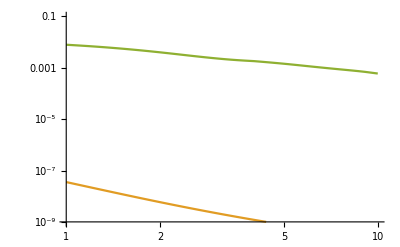

```mathematica
LogLogPlot[{σSM[x TeV],σOneLoopSM[x TeV],σMissingEnergy[x TeV],σqqMisTag[(x TeV)]},{x,1,10},AxesLabel->{"\\sqrt{s} / TeV"//MaTeX,"\\sigma / pb"//MaTeX},PlotLegends->{"\\sigma_{SM}"//MaTeX, "\\sigma_{OneLoop}"//MaTeX,"\\sigma_{\\nu \\nu}"//MaTeX, "\\sigma_{qq}"//MaTeX},PlotRange->{10^-9,0.1}]
```

```mathematica
AFBSM[eCM_,Pp_:0,Pm_:0]:=AFBqq[eCM,Pp,Pm]
```

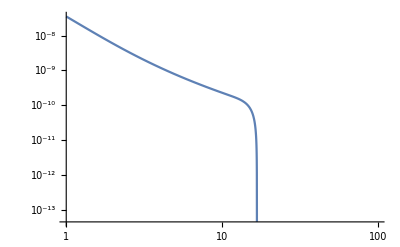

```mathematica
LogLogPlot[{σOneLoopSM[x TeV]},{x,1,100}]
```

## A_FB: Combined Statistics

## Computation of the A_FB

```mathematica
CPAFB[eCM_:defaultScale,Pp_:0,Pm_:0,lumi_:defaultLumi,c_:0.7,c9_:C9bench,c10_:C10bench,Cp9_:0,Cp10_:0,CS_:0,CP_:0,CpS_:0,CpP_:0]:=With[{Fs=BBbarFactor*σNPF[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP],Bs=BBbarFactor*σNPB[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP],Fb=σqqF[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP],Bb=σqqB[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP]},
(Fs+Fb-Bs-Bb)/(Fs+Fb+Bs+Bb)];
```

```mathematica
AFB[eCM_:defaultScale,Pp_:0,Pm_:0,lumi_:defaultLumi,c_:0.7,c9_:C9bench,c10_:C10bench,Cp9_:0,Cp10_:0,CS_:0,CP_:0,CpS_:0,CpP_:0]=With[{Fs=σNPF[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP],Bs=σNPB[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP],Fb=σqqF[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP],Bb=σqqB[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP]},With[{NFsig=lumi*(*ϵb(1-ϵs) deleting the other flavor tagging stuff in the AFB - the "bsMistag" takes care of this factor in the cross section definitions*)(Fs*c+Bs(1-c)),NBsig=lumi(*ϵb(1-ϵs)*)(Bs*c+Fs(1-c)),NbarFsig=(*ϵb(1-ϵs)*)lumi(Bs*c+Fs(1-c)),NbarBsig=(*ϵb(1-ϵs)*)lumi(Fs*c+Bs(1-c)),NFbkg=(lumi/2)(Fb*c+Bb(1-c)),NBbkg=(lumi/2)(Bb*c+Fb(1-c)),NbarFbkg=(lumi/2)(Bb*c+Fb(1-c)),NbarBbkg=(lumi/2)(Fb*c+Bb(1-c))},
With[{NFtot=NFsig+NbarBsig+NFbkg+NbarBbkg,NBtot=NBsig+NbarFsig+NBbkg+NbarFbkg},
(NFtot-NBtot)/(NFtot+NBtot)
]
]
]//Simplify;
(*Using the fact that forward Bbar events are equal to the backward B events. The qqbar events already have charge tagging baked into their definition in an above section. The factor of (1/2) in the backgrounds is to remove the factor of 2 in the 2 ϵ(1-ϵ) prescription in the earlier section. That was because either jet could have been mistagged as a b, but now we actually care to couple that to the charge tagging case.*)
```

```mathematica
With[{NFsig=lumi(Fs*c+Bs(1-c)),NBsig=lumi(Bs*c+Fs(1-c)),NbarFsig=lumi(Bs*c+Fs(1-c)),NbarBsig=lumi(Fs*c+Bs(1-c)),NFbkg=(lumi/2)(Fb*c+Bb(1-c)),NBbkg=(lumi/2)(Bb*c+Fb(1-c)),NbarFbkg=(lumi/2)(Bb*c+Fb(1-c)),NbarBbkg=(lumi/2)(Fb*c+Bb(1-c))},
With[{NFtot=NFsig+NbarBsig+NFbkg+NbarBbkg,NBtot=NBsig+NbarFsig+NBbkg+NbarFbkg},
(NFtot-NBtot)/(NFtot+NBtot)
]
]//Simplify
```

-((2 c-1) (Bb+2 Bs-Fb-2 Fs))/(Bb+2 Bs+Fb+2 Fs)

## Uncertainty - Theory

The collider observed forward backward asymmetry is given by A_FB = (N_F^s+N_F^b-N_B^s-N_B^b)/(N_F^s+N_F^b+N_B^s+N_B^b), where the “s” and “b” superscripts stand for the signal and background rates. However, when summed over the B_s and (B̄)_s production modes, the predicted forward backward asymmetry vanishes, for both the signal and the background, weakening its role as a test variable. As such, in order to not waste any statistics, we consider the separation of each production mode by the procedure of charge tagging. We then consider a related object, the CP-averaged forward backward asymmetry (Ã)_FB, defined by the following formula
(Ã)_FB = (n_F + (n̄)_B - n_B - (n̄)_F)/(n_F + (n̄)_B + n_B + (n̄)_F),
where n_D represented the total number of B_s production events in the direction D ∈ {F, B}, and (n̄)_D its (B̄)_s production counterpart. In this section, barred/overlined variables will consistently be used in an analogous way.
The uncertainties on the individual numbers used above (see TEX file - To B or μ to B) experience the following bounds:
σ_(n_D^obs)^2 ≤ ((σ_D c + (σ̄)_D(1-c))/(σ_D + (σ̄)_D))^2 (N_D^s + 2 N_D^b) + (c (1-c))/(σ_D + (σ̄)_D) (c^2 σ_D + (1-c)^2 (σ̄)_D + 2c (1-c)√(σ_D(σ̄)_D)) N_D
σ_((n̄)_D^obs)^2 ≤ (((σ̄)_D c + σ_D(1-c))/(σ_D + (σ̄)_D))^2 (N_D^s + 2 N_D^b) + (c (1-c))/(σ_D + (σ̄)_D) (c^2(σ̄)_D + (1-c)^2 σ_D + 2c (1-c)√(σ_D(σ̄)_D)) N_D
where c is the (Bernoulli/Binomial) probability of correctly identifying the charge of the b-jet (assuming that it has been successfully flavor/flavour tagged), σ_D is the restriction of the  cross section to the region D, and N_D= n_D + (n̄)_D is the total number of events in that direction. The s and b superscripts refer to the signal and background. The factor of 2 accompanying N_D^b follows from the conditioning of the total number of production events truly representing the sum of the new physics and the background, as well as the theoretical prediction for new physics equalling the total number of observed events without the background events. In the estimate of the error for (Ã)_FB, we shall conservatively saturate the bound above.
Taking its derivative, d(Ã)_FB = (∂(Ã)_FB)/(∂ n_F)dn_F + ...
The error propagation replaces this with a finite approximation, dn_F ~ δn_F
Thus, δ(Ã)_FB ≃ (∂(Ã)_FB)/(∂ n_F) σ_(n_F^obs) ⊕  (∂(Ã)_FB)/(∂ n_B) σ_(n_B^obs) ⊕ (∂(Ã)_FB)/(∂ (n̄)_F) σ_((n̄)_F^obs) ⊕  (∂(Ã)_FB)/(∂ (n̄)_B) σ_((n̄)_B^obs) , where the statistical nature of the errors forces us to use ⊕, the sum in quadrature.
We use the result ∂_x  (±x+n)/(x+d) = 2(±d - n)/(x+d)^2 
The denominator is always 1/N_Tot^2. Thus, the error expression becomes δ(Ã)_FB = 2/N_Total^2 √((σ_(n_F^obs)^2+σ_((n̄)_B^obs)^2)(n_B+(n̄)_F)^2+(σ_(n_B^obs)^2+σ_((n̄)_F^obs)^2)(n_F+(n̄)_B)^2)

## Computation of the Uncertainty

```mathematica
systematicUncertaintyFactor[sigma_,lumi_:defaultLumi,sysUnc_:systematicUncertainty]=(sigma*lumi*sysUnc)^2;
```

```mathematica
VEprefac[sigma1_,sigma2_,c_:0.7]=((sigma1*c+sigma2*(1-c))/(sigma1+sigma2))^2;
EVprefac[sigma1_,sigma2_,c_:0.7]=((c(1-c))/(sigma1+sigma2))(c^2 sigma1+(1-c)^2 sigma2+2c(1-c)√(sigma1 sigma2));
Clear[VarianceCPAFB]
Clear[σCPAFB]
VarianceCPAFB[σFs_,σBs_,σFb_,σBb_,c_:0.7,lumi_:defaultLumi]=With[{σF=σFs+σFb,σB=σBs+σBb},(4/lumi)(1/(σF+σB)^4)((2σB)^2(2*(VEprefac[σF,σB,c](σFs+(*2*)σFb+systematicUncertaintyFactor[σFb,√lumi])+EVprefac[σF,σB,c]σF))+(2σF)^2(2*(VEprefac[σB,σF,c](σBs+(*2*)σBb+systematicUncertaintyFactor[σBb,√lumi])+EVprefac[σB,σF,c]σB)))]//Simplify;
σCPAFB[eCM_:defaultScale,Pp_:0,Pm_:0,lumi_:defaultLumi,c_:0.7,c9_:C9bench,c10_:C10bench,Cp9_:0,Cp10_:0,CS_:0,CP_:0,CpS_:0,CpP_:0]:=With[{Fs=σNPF[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP],Bs=σNPB[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP],Fb=σqqF[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP],Bb=σqqB[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP]},
(2c-1)√VarianceCPAFB[Fs,Bs,Fb,Bb,c,lumi]];
```

## Conservative Upper Bound on Error

```mathematica
deltaCPAFB[eCM_:defaultScale,Pp_:0,Pm_:0,lumi_:defaultLumi,c_:0.7,c9_:C9bench,c10_:C10bench,Cp9_:0,Cp10_:0,CS_:0,CP_:0,CpS_:0,CpP_:0]:=With[{Fs=BBbarFactor*σNPF[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP],Bs=BBbarFactor*σNPB[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP],Fb=σqqF[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP],Bb=σqqB[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP]},
(2 /(lumi(2c-1)(Fs+Bs)^2))(((Fs^2(Bs+2Bb+lumi(systematicUncertainty*Bb)^2)+Bs*(Fs+2Fb+lumi(systematicUncertainty*Fb)^2)))lumi)^(1/2)];
```

```mathematica
δAFB[eCM_:defaultScale,Pp_:0,Pm_:0,lumi_:defaultLumi,c_:0.7,c9_:C9bench,c10_:C10bench,Cp9_:0,Cp10_:0,CS_:0,CP_:0,CpS_:0,CpP_:0]:=With[{Fs=σNPF[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP],Bs=σNPB[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP],Fb=σqqF[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP],Bb=σqqB[eCM,Pp,Pm,c9,c10,Cp9,Cp10,CS,CP,CpS,CpP]},With[{NFsig=lumi*ϵb(1-ϵs)(Fs*c+Bs(1-c)),NBsig=lumi*ϵb(1-ϵs)(Bs*c+Fs(1-c)),NbarFsig=lumi*ϵb(1-ϵs)(Bs*c+Fs(1-c)),NbarBsig=lumi*ϵb(1-ϵs)(Fs*c+Bs(1-c)),NFbkg=(lumi/2)(Fb*c+Bb(1-c)),NBbkg=(lumi/2)(Bb*c+Fb(1-c)),NbarFbkg=(lumi/2)(Bb*c+Fb(1-c)),NbarBbkg=(lumi/2)(Fb*c+Bb(1-c))},
With[{NFtot=(NFsig+NbarBsig+NFbkg+NbarBbkg)//Simplify,NBtot=(NBsig+NbarFsig+NBbkg+NbarFbkg)//Simplify},
(2/(NFtot+NBtot)^2)√((NFtot(1+systematicUncertainty^2 NFtot)(*Within this paranthesis is δNFtot^2*))NBtot^2+(NBtot(1+systematicUncertainty^2 NBtot))NFtot^2)
]
]
]//Simplify;
```

```mathematica
BBbarFactor*σNPF[10^4,0,0]*defaultLumi
BBbarFactor*σNPB[10^4,0,0]*defaultLumi
σqqF[10^4,0,0]*defaultLumi
σqqB[10^4,0,0]*defaultLumi
```

363.99

596.466

147.979

631.988

```mathematica
δAFB[6TeV,0,0,4*10^6]
δAFB[10TeV,0,0,10^6]
δAFB[10TeV,0,0,10^7]
AFB[10TeV,0,0,10^7,0.7]
AFB[10TeV,0,0,10^6,0.7]
AFB[6TeV,0,0,4*10^6,0.7]
```

0.0166459

0.0292777

0.0159509

-0.164669

-0.164669

-0.227392

## Confidence Intervals and Event Data

## Relevant Functions

```mathematica
invAttobarns=1;(*Expected luminosity. This is the smallest of the scenarios painted in 2103.01617: (TeV, ab^-1): {(3, 1), (6, 4), (10, 10)}.*)
targetLuminosity=10^6*invAttobarns;(*Conversion to pico, to match cross sections.*)
(*stdev[polPlus_:0,polMin_:0,eCM_:defaultScale,lumi_:defaultLumi]=√(σSMpolarized[eCM,polPlus,polMin]*lumi);(*Fairly clear.*)
c9c10[C9_:C9bench,C10_:C10bench,Pp_:0,Pm_:0,eCM_:defaultScale,lumi_:defaultLumi]=σNP[eCM,Pp,Pm,C9,C10]*lumi;(*All other coefficients are 0 by default. The first 2 0s are indicating an unpolarized signal. √s = 9TeV*)

GlobalUncertainty[C9_:C9bench,C10_:C10bench,polPlus_:0,polMin_:0,eCM_:defaultScale,lumi_:defaultLumi]:=√((σNP[eCM,polPlus,polMin,C9,C10,0,0,0,0,0,0]+2*σSMpolarized[eCM,polPlus,polMin]+systematicUncertainty^2 σSMpolarized[eCM,polPlus,polMin]^2*lumi)*lumi);*)
```

```mathematica
errorNevents[eCM_:defaultScale,Pp_:0,Pm_:0,c9_:C9bench,c10_:C10bench,lumi_:defaultLumi]=√(lumi*(BBbarFactor*σNP[eCM,Pp,Pm,c9,c10]+σSMpolarized[eCM,Pp,Pm,c9,c10](2+σSMpolarized[eCM,Pp,Pm,c9,c10]*systematicUncertainty^2*lumi)));

NdiscrepancyBench[eCM_:defaultScale,Pp_:0,Pm_:0,c9_:C9bench,c10_:C10bench,lumi_:defaultLumi]=Abs[lumi*BBbarFactor*(σNP[eCM,Pp,Pm,c9,c10]-σNP[eCM,Pp,Pm,C9collider[eCM],C10collider[eCM]])];

CPAFBdiscrepancyBench[eCM_:defaultScale,Pp_:0,Pm_:0,c9_:C9bench,c10_:C10bench,lumi_:defaultLumi,c_:0.7]=Abs[(CPAFB[eCM,Pp,Pm,lumi,c,c9,c10]-CPAFB[eCM,Pp,Pm,lumi,c,C9collider[eCM],C10collider[eCM]])];

combinedErr[eCM_:defaultScale,PpAFB_:0,PmAFB_:0,Ppσ_:0,Pmσ_:0,c9_:C9bench,c10_:C10bench,lumi_:defaultLumi,c_:0.7]:=√((CPAFBdiscrepancyBench[eCM,PpAFB,PmAFB,lumi,c,c9,c10]/σCPAFB[eCM,PpAFB,PmAFB,lumi,c,c9,c10])^2+(NdiscrepancyBench[eCM,Ppσ,Pmσ,c9,c10,lumi]/errorNevents[eCM,Ppσ,Pmσ,c9,c10,lumi])^2);

AFBdiscrepancyBench[eCM_:defaultScale,Pp_:0,Pm_:0,lumi_:defaultLumi,c_:0.7,c9_:C9bench,c10_:C10bench]:=Abs[(AFB[eCM,Pp,Pm,lumi,c,c9,c10]-AFB[eCM,Pp,Pm,lumi,c,C9collider[eCM],C10collider[eCM]])];
combinedErrOverestimate[eCM_:defaultScale,PpAFB_:0,PmAFB_:0,Ppσ_:0,Pmσ_:0,c9_:C9bench,c10_:C10bench,lumi_:defaultLumi,c_:0.7]:=√((AFBdiscrepancyBench[eCM,PpAFB,PmAFB,lumi,c,c9,c10]/δAFB[eCM,PpAFB,PmAFB,lumi,c,c9,c10])^2+(NdiscrepancyBench[eCM,Ppσ,Pmσ,c9,c10,lumi]/errorNevents[eCM,Ppσ,Pmσ,c9,c10,lumi])^2);
```

```mathematica
AFBdiscrepancyBench[10^4,0,0,1.9,0.2]
σCPAFB[10^4,0,0,defaultLumi,0.7,1,0.2]
NdiscrepancyBench[10^4,0,0,1,0.2]
errorNevents[10^4,0,0,1,0.2]
```

0.

0.0176802

383.727

56.1022

## Event Data

```mathematica
NtotalEvents10TeV1invab=(BBbarFactor*σNP[10TeV,0,0]+σqqMisTagpol[10TeV,0,0])*defaultLumi
NbkgEvents10TeV1invab=(σqqMisTagpol[10TeV,0,0])*defaultLumi
σNtotalEvents10TeV1invab=errorNevents[10TeV,0,0]
σNbkgEvents10TeV1invab=errorNevents[10TeV,0,0,0,0,defaultLumi]
```

1740.42

779.967

52.5712

42.465

```mathematica
NtotalEvents10TeV10invab=(BBbarFactor*σNP[10TeV,0,0]+σqqMisTagpol[10TeV,0,0])*10^7
NbkgEvents10TeV10invab=(σqqMisTagpol[10TeV,0,0])*10^7
σNtotalEvents10TeV10invab=errorNevents[10TeV,0,0,C9bench,C10bench,10^7]
σNbkgEvents10TeV10invab=errorNevents[10TeV,0,0,0,0,10^7]
```

17404.2

7799.67

222.571

199.833

```mathematica
NtotalEvents6TeV4invab=(BBbarFactor*σNP[6TeV,0,0]+σqqMisTagpol[6TeV,0,0])*4*10^6
NbkgEvents6TeV4invab=(σqqMisTagpol[6TeV,0,0])*4*10^6
σNtotalEvents6TeV4invab=errorNevents[6TeV,0,0,C9bench,C10bench,4*10^6]
σNbkgEvents6TeV4invab=errorNevents[6TeV,0,0,0,0,4*10^6]
```

10050.5

8667.45

220.834

217.68

```mathematica
NtotalEvents10TeV1invabPol=(BBbarFactor*σNP[10TeV,-0.5,0.5]+σqqMisTagpol[10TeV,-0.5,0.5])*defaultLumi
NbkgEvents10TeV1invabPol=(σqqMisTagpol[10TeV,-0.5,0.5])*defaultLumi
σNtotalEvents10TeV1invabPol=errorNevents[10TeV,-0.5,0.5]
σNbkgEvents10TeV1invabPol=errorNevents[10TeV,-0.5,0.5,0,0,defaultLumi]
```

1485.26

594.663

47.1315

36.4798

```mathematica
NtotalEvents10TeV10invabPol=(BBbarFactor*σNP[10TeV,-0.5,0.5]+σqqMisTagpol[10TeV,-0.5,0.5])*10^7
NbkgEvents10TeV10invabPol=(σqqMisTagpol[10TeV,-0.5,0.5])*10^7
σNtotalEvents10TeV10invabPol=errorNevents[10TeV,-0.5,0.5,C9bench,C10bench,10^7]
σNbkgEvents10TeV10invabPol=errorNevents[10TeV,-0.5,0.5,0,0,10^7]
```

14852.6

5946.63

186.934

161.364

```mathematica
NtotalEvents6TeV4invabPol=(BBbarFactor*σNP[6TeV,-0.5,0.5]+σqqMisTagpol[6TeV,-0.5,0.5])*4*10^6
NbkgEvents6TeV4invabPol=(σqqMisTagpol[6TeV,-0.5,0.5])*4*10^6
σNtotalEvents6TeV4invabPol=errorNevents[6TeV,-0.5,0.5,C9bench,C10bench,4*10^6]
σNbkgEvents6TeV4invabPol=errorNevents[6TeV,-0.5,0.5,0,0,4*10^6]
```

7890.56

6608.09

178.789

175.166

```mathematica
14852-5947
√(187^2+161^2)//N
```

8905

246.759

## Confidence Intervals (Single Coefficient) and Probed Scales

```mathematica
scaleFromUncertainty[σ_]=(4/(√2)GFermi Vtb Vts αEM/(4π)σ)^(-1/2)/(1000(*Switch to TeV*));
uncertaintyFromScale=InverseFunction[scaleFromUncertainty];
scaleFromUncertainty[0.22]
```

75.0906

### Uncertainty Radius - Muon Collider Analysis

We pretend that there is no new physics here, and essentially look at ((N^NP+N^bkg)-N^bkg)/(σ_(N^bkg)) = 2 to evaluate the 2 σ confidence interval of each coefficient being zero. Effectively, how large does each individual coefficient have to be for it to no longer be explained by uncertainties on the background. We expect all the vectors to have the same interval, and the scalars to have the same interval, since the cross section depends on them in the same way. The 8 below this are at 10 TeV, 1/ab.

```mathematica
intervalLumi=10^6;
```

```mathematica
C9radius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[10 TeV,0,0,r,0,0,0,0,0,0,0])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
C10radius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,r,0,0,0,0,0,0])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
Cp9radius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,0,r,0,0,0,0,0])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
Cp10radius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,0,0,r,0,0,0,0])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
```

{{r→0.222487}}

{{r→0.222487}}

{{r→0.222487}}

«1 more identical outputs»

```mathematica
CSradius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,0,0,0,r,0,0,0])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
CPradius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,0,0,0,0,r,0,0])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
CpSradius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,0,0,0,0,0,r,0])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
CpSPradius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,0,0,0,0,0,0,r])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
```

{{r→0.256905}}

{{r→0.256905}}

{{r→0.256905}}

«1 more identical outputs»

We now evaluate the same intervals, but for the HL-LHC at 10/ab;

```mathematica
intervalLumi=10^7;
```

```mathematica
C9radius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[10 TeV,0,0,r,0,0,0,0,0,0,0])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
C10radius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,r,0,0,0,0,0,0])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
Cp9radius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,0,r,0,0,0,0,0])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
Cp10radius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,0,0,r,0,0,0,0])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
```

{{r→0.166549}}

{{r→0.166549}}

{{r→0.166549}}

«1 more identical outputs»

```mathematica
CSradius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,0,0,0,r,0,0,0])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
CPradius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,0,0,0,0,r,0,0])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
CpSradius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,0,0,0,0,0,r,0])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
CpSPradius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,0,0,0,0,0,0,r])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
```

{{r→0.192314}}

{{r→0.192314}}

{{r→0.192314}}

«1 more identical outputs»

This will be for 6 TeV at 4 ab^-1.

```mathematica
intervalLumi=4*10^6;
```

```mathematica
C9radius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[6 TeV,0,0,r,0,0,0,0,0,0,0])/(√(σSMpolarized[6TeV,0,0](1+σSMpolarized[6TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
CSradius=Quiet@Solve[(intervalLumi*BBbarFactor*σNP[6 TeV,0,0,0,0,0,0,r,0,0,0])/(√(σSMpolarized[6TeV,0,0](1+σSMpolarized[6TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))==2,r,PositiveReals]
```

{{r→0.45983}}

{{r→0.530966}}

We also evaluate a χ^2 goodness in the same way, simply including the A_FB.

```mathematica
intervalLumi=10^6;
```

```mathematica
Vectorχ2radius=Quiet@Solve[√(((AFB[10TeV,0,0,intervalLumi,0.7,r,0,0,0,0,0,0,0]-AFB[10TeV,0,0,intervalLumi,0.7,0,0,0,0,0,0,0,0])/δAFB[10TeV,0,0,intervalLumi,0.7,0,0])^2+((intervalLumi*BBbarFactor*σNP[10 TeV,0,0,r,0,0,0,0,0,0,0])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi)))^2)==√6,r,PositiveReals]
Scalarχ2radius=Quiet@Solve[√(((AFB[10TeV,0,0,intervalLumi,0.7,0,0,0,0,0,0,0,r]-AFB[10TeV,0,0,intervalLumi,0.7,0,0,0,0,0,0,0,0])/δAFB[10TeV,0,0,intervalLumi,0.7,0,0])^2+((intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,0,0,0,0,0,0,r])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi)))^2)==Sqrt[6],r,PositiveReals]
```

{{r→0.242525}}

{{r→0.280043}}

```mathematica
intervalLumi=10^7;
```

```mathematica
Vectorχ2radius=Quiet@Solve[√(((AFB[10TeV,0,0,intervalLumi,0.7,r,0,0,0,0,0,0,0]-AFB[10TeV,0,0,intervalLumi,0.7,0,0,0,0,0,0,0,0])/δAFB[10TeV,0,0,intervalLumi,0.7,0,0])^2+((intervalLumi*BBbarFactor*σNP[10 TeV,0,0,r,0,0,0,0,0,0,0])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi)))^2)==2.3,r,PositiveReals]
Scalarχ2radius=Quiet@Solve[√(((AFB[10TeV,0,0,intervalLumi,0.7,0,0,0,0,0,0,0,r]-AFB[10TeV,0,0,intervalLumi,0.7,0,0,0,0,0,0,0,0])/δAFB[10TeV,0,0,intervalLumi,0.7,0,0])^2+((intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,0,0,0,0,0,0,r])/(√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi)))^2)==2.3,r,PositiveReals]
```

{{r→0.174418}}

{{r→0.201401}}

### Scales - Muon Collider Analysis

```mathematica
Λvec1abMC=scaleFromUncertainty[0.2224866074253918(*Taken from Confidence intervals (single coeff)*)]
Λscalar1abMC=scaleFromUncertainty[0.2569054053762731]
Λvec10abMC=scaleFromUncertainty[0.16654911762402597(*Taken from Confidence intervals (single coeff)*)]
Λscalar10abMC=scaleFromUncertainty[0.19231435578705208]
```

74.6698

69.4881

86.303

80.314

### Scales - Flavio Fits: LHC-b Data

```mathematica
(*Current Data*)
(*b -> s decays*)
ΛbsC9current=49(*TeV*);
ΛbsC10current=61(*TeV*);
ΛbsCp9current=51(*TeV*);
ΛbsCp10current=59(*TeV*);
ΛbsCScurrent=411(*TeV*);

(*HL LHC Projected Data*)
(*b -> s decays*)
ΛbsC9future=114(*TeV*);
ΛbsC10future=128(*TeV*);
ΛbsCp9future=115(*TeV*);
ΛbsCp10future=125(*TeV*);
ΛbsCSfuture=614(*TeV*);
```

```mathematica
(*Current Data*)
(*b -> d decays*)
ΛbdC10current=45(*TeV*);
ΛbdCp10current=45(*TeV*);
ΛbdCScurrent=341(*TeV*);

(*HL LHC Projected Data*)
(*b -> d decays*)
ΛbdC9future=121(*TeV*);
ΛbdC10future=139(*TeV*);
ΛbdCp9future=121(*TeV*);
ΛbdCp10future=139(*TeV*);
ΛbdCSfuture=850(*TeV*);
```

### HL-LHC and Muon Collider Joint Analysis - Radius and Scale

We will use the uncertainty from scale function (next section) to determine a set of uncertainties (2 σ radius) from the scales generated in Flavio

```mathematica
(*1/ab and HL-LHC used*)
intervalLumi=10^6;
```

```mathematica
{C9radius,C10radius,Cp9radius,Cp10radius,CSradius}=uncertaintyFromScale/@{ΛbsC9current,ΛbsC10current,ΛbsCp9current,ΛbsCp10current,ΛbsCScurrent}
```

{0.516657,0.333376,0.476929,0.356361,0.00734362}

```mathematica
jointC9radius=r/.Quiet@Solve[((intervalLumi*BBbarFactor*σNP[10 TeV,0,0,r,0,0,0,0,0,0,0])/√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))^2+(r/(C9radius/2(*The provided radius was 2 σ, not 1 σ*)))^2==2^2(*(2 σ)^2 = 4 σ^2*),r,PositiveReals][[1]]
ΛjointC9current1ab=scaleFromUncertainty@jointC9radius
```

0.212422

76.4184

```mathematica
jointCSradius=r/.Quiet@Solve[((intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,0,0,0,r,0,0,0])/√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))^2+(r/(CSradius/2))^2==2^2(*(2 σ)^2 = 4 σ^2*),r,PositiveReals][[1]]
ΛjointCScurrent1ab=scaleFromUncertainty@jointCSradius
```

0.00734362

411.

```mathematica
(*10/ab and HL-LHC projections used*)
intervalLumi=10^7;
```

```mathematica
{C9radius,C10radius,Cp9radius,Cp10radius,CSradius}=uncertaintyFromScale/@{ΛbsC9future,ΛbsC10future,ΛbsCp9future,ΛbsCp10future,ΛbsCSfuture}
```

{0.0954519,0.0757136,0.093799,0.0793915,0.00329047}

```mathematica
jointC9radius=r/.Quiet@Solve[((intervalLumi*BBbarFactor*σNP[10 TeV,0,0,r,0,0,0,0,0,0,0])/√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))^2+(r/(C9radius/2(*The provided radius was 2 σ, not 1 σ*)))^2==2^2(*(2 σ)^2 = 4 σ^2*),r,PositiveReals][[1]]
ΛjointC9future10ab=scaleFromUncertainty@jointC9radius
```

0.0910828

116.702

```mathematica
jointCSradius=r/.Quiet@Solve[((intervalLumi*BBbarFactor*σNP[10 TeV,0,0,0,0,0,0,r,0,0,0])/√(σSMpolarized[10TeV,0,0](1+σSMpolarized[10TeV,0,0]*systematicUncertainty^2*intervalLumi)*intervalLumi))^2+(r/(CSradius/2))^2==2^2(*(2 σ)^2 = 4 σ^2*),r,PositiveReals][[1]]
ΛjointCSfuture10ab=scaleFromUncertainty@jointCSradius
```

0.00329047

614.

## Χ^2(C_9,C_10) Confidence Intervals (Quadratic Approximation)

We will compute the covariance matrix C by using a quadratic approximation to the "χ^2" function. Let x, y replace C_9 and C_10. Then, we consider f(x,y)=(N(x,y) - N(x̄,ȳ))^2/δN^2 + (A_FB(x,y) - A_FB(x̄,ȳ))^2/δA_FB^2 ≃ (x-x̄ | y-ȳ) C^-1(x-x̄
y-ȳ), with the goal of finding the elements of C^-1. Computing the Hessian of f, and evaluating it at (x,y) = (x̄,ȳ) grants us 2 C^-1, as taking 2 derivatives of the RHS will demonstrate.

```mathematica
vecEG={{x-xb,y-yb}}//Transpose;
matEG={{invC11,invC12},{invC21,invC22}};
D[Transpose[vecEG].matEG.vecEG,x,y]
D[Transpose[vecEG].matEG.vecEG,x,x]
D[Transpose[vecEG].matEG.vecEG,y,y]
```

(invC12+invC21)

(2 invC11)

(2 invC22)

```mathematica
chisq[lumi_:defaultLumi,c9_:C9bench,c10_:C10bench]=Simplify[combinedErrOverestimate[10TeV,0,0,0,0,c9,c10,lumi,0.7]^2,Assumptions->{c9∈Reals,c10∈Reals}]/.{Abs[input___]->Identity[input](*Allows us to take derivatives. The absolute value thing is squared, and only matters for complex c9, c10.*)};
```

```mathematica
covInverse10TeVmat[lumi_:defaultLumi]={{mat11,mat12},{mat12,mat22}}/.{mat11->Limit[1/2(D[chisq[lumi,c9,c10],{c9,2}]//Simplify),{c9->C9bench,c10->C10bench}]//Simplify,mat22->Limit[1/2(D[chisq[lumi,c9,c10],{c10,2}]//Simplify),{c9->C9bench,c10->C10bench}]//Simplify,mat12->Limit[1/2(D[chisq[lumi,c9,c10],c9,c10]//Simplify),{c9->C9bench,c10->C10bench}]//Simplify};
cov10TeVmat[lumi_:defaultLumi]=Inverse@covInverse10TeVmat[lumi];
```

```mathematica
cov1ab10TeV=cov10TeVmat[]
δc9$1ab=√cov1ab10TeV[[1,1]]
δc10$1ab=√cov1ab10TeV[[2,2]]
ρ$1ab=cov1ab10TeV[[1,2]]/(δc9$1ab δc10$1ab)
```

(0.00067314 | 0.000835972
0.000835972 | 0.00640077)

0.025945

0.0800048

0.402738

```mathematica
cov10ab10TeV=cov10TeVmat[10^7]
δc9$10ab=√cov10ab10TeV[[1,1]]
δc10$10ab=√cov10ab10TeV[[2,2]]
ρ$10ab=cov10ab10TeV[[1,2]]/(δc9$10ab δc10$10ab)
```

(0.000141057 | 0.000272891
0.000272891 | 0.00188944)

0.0118768

0.0434677

0.528597

```mathematica
cov10TeVInfLumi=Limit[cov10TeVmat[Lumi],{Lumi->∞}]
δc9$limit=√cov10TeVInfLumi[[1,1]]
δc10$limit=√cov10TeVInfLumi[[2,2]]
ρ$limit=cov10TeVInfLumi[[1,2]]/(δc9$limit δc10$limit)
```

(0.0000819368 | 0.000210327
0.000210327 | 0.00138818)

0.0090519

0.0372583

0.623636

## NP Precision

```mathematica
unpolPrecision1ab=(defaultLumi*BBbarFactor*σNP[10 TeV,0,0])/errorNevents[10TeV,0,0,C9bench,C10bench,defaultLumi]
unpolPrecision1abPercent=100/unpolPrecision1ab
```

18.2696

5.47357

```mathematica
unpolPrecision10ab=(10^7*BBbarFactor*σNP[10 TeV,0,0])/errorNevents[10TeV,0,0,C9bench,C10bench,10^7]
unpolPrecision10abPercent=100/unpolPrecision10ab
```

43.1528

2.31735

```mathematica
unpolPrecision4ab6TeV=(4*10^6*BBbarFactor*σNP[6 TeV,0,0])/errorNevents[6TeV,0,0,C9bench,C10bench,4*10^6]
unpolPrecision4ab6TeVPercent=100/unpolPrecision4ab6TeV
```

6.26287

15.9671

```mathematica
polPrecision1ab=(defaultLumi*BBbarFactor*σNP[10 TeV,-0.5,0.5])/errorNevents[10TeV,-0.5,0.5,C9bench,C10bench,defaultLumi]
polPrecision1abPercent=100/polPrecision1ab
```

18.8961

5.29209

```mathematica
polPrecision10ab=(10^7*BBbarFactor*σNP[10 TeV,-0.5,0.5])/errorNevents[10TeV,-0.5,0.5,C9bench,C10bench,10^7]
polPrecision10abPercent=100/polPrecision10ab
```

47.6426

2.09896

```mathematica
polPrecision4ab6TeV=(4*10^6*BBbarFactor*σNP[6 TeV,-0.5,0.5])/errorNevents[6TeV,-0.5,0.5,C9bench,C10bench,4*10^6]
polPrecision4ab6TeVPercent=100/polPrecision4ab6TeV
```

7.17308

13.941

```mathematica
unpolPrecision1abOldBenchmarks=(defaultLumi*BBbarFactor*σNP[10 TeV,0,0,-0.35,0.35])/errorNevents[10TeV,0,0,-0.35,0.35,defaultLumi]
unpolPrecision1abOldBenchmarksPercent=100/unpolPrecision1abOldBenchmarks
polPrecision1abOldBenchmarks=(defaultLumi*BBbarFactor*σNP[10 TeV,-0.5,0.5,-0.35,0.35])/errorNevents[10TeV,-.5,0.5,-0.35,0.35,defaultLumi]
polPrecision1abOldBenchmarksPercent=100/polPrecision1abOldBenchmarks
```

6.87749

14.5402

2.10829

47.4317

## Plots

## √s plot(s)

```mathematica
(*oneσcolour=Black;
twoσcolour=Black;
oneσshade=Red;
twoσshade=Red;
σ1opacity=0.6;
σ2opacity=.1;
allPlot=LogLogPlot[{σSMpolarized[x TeV],σOneLoopSM[x TeV],σMissingEnergy[x TeV],σqqMisTagpol[(x TeV)],σNP[x TeV],σNP[x TeV,0,0,C9upper2σblow,C10upper2σblow],σNP[x TeV,0,0,C9lower2σblow,C10lower2σblow],σNP[x TeV,0,0,C9upper1σblow,C10upper1σblow],σNP[x TeV,0,0,C9lower1σblow,C10lower1σblow]},{x,1,15},FrameLabel->{"\\sqrt{s} / TeV"//MaTeX,"\\sigma / pb"//MaTeX},PlotLegends->{"\\sigma_{Background}"//MaTeX, "\\sigma_{1\, \\text{Loop}}"//MaTeX,"\\sigma_{\\nu \\nu}"//MaTeX, "\\sigma_{qq}"//MaTeX, "\\sigma_{NP}"//MaTeX},PlotRange->{10^-9,0.1},Filling->{{6->{{5},Directive[Opacity[0.1,Red]]}},{7->{{5},Directive[Opacity[0.1,Red]]}}},PlotStyle->{Bold,Bold,Bold,Bold,Bold,{Dashed,twoσcolour},{Dashed,twoσcolour},{Dashed,oneσcolour},{Dashed,oneσcolour}},Frame->True,PlotRangePadding->0.01]*)
(*No RG Flows, the upper and lower stuff is evaluated at the low scale.*)
```

```mathematica
(*Export["testRootSPlot.pdf",allPlot]*)
```

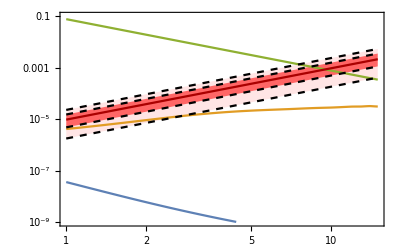

```mathematica
oneσcolour=Black;
twoσcolour=Black;
oneσshade=Red;
twoσshade=Red;
σ1opacity=0.6;
σ2opacity=.1;
RGflowRootSPlot=LogLogPlot[{(*σSMpolarized[x TeV],*)σOneLoopSM[x TeV],(*σMissingEnergy[x TeV]*)σMissingνν[x TeV],σqqMisTagpol[(x TeV)],BBbarFactor σNP[x TeV],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9upper2σblow,C10upper2σblow],C10collider[x TeV,C9upper2σblow,C10upper2σblow]],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9lower2σblow,C10lower2σblow],C10collider[x TeV,C9lower2σblow,C10lower2σblow]],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9upper1σblow,C10upper1σblow],C10collider[x TeV,C9upper1σblow,C10upper1σblow]],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9lower1σblow,C10lower1σblow],C10collider[x TeV,C9lower1σblow,C10lower1σblow]]},{x,1,15},FrameLabel->{"\\sqrt{s} / \\text{TeV}"//MaTeX,"\\sigma / \\text{pb}"//MaTeX},PlotLegends->{(*"\\sigma_{\\text{Background}}"//MaTeX,*) "\\sigma_{1\, \\text{Loop}}"//MaTeX,"\\sigma_{\\text{VBF}}"//MaTeX, "\\sigma_{qq}"//MaTeX, "\\sigma_{\\text{NP}}"//MaTeX},PlotRange->{10^-9,0.1},Filling->{{5->{{7},Directive[Opacity[σ2opacity,twoσshade]]}},{6->{{8},Directive[Opacity[σ2opacity,twoσshade]]}},{7->{{4},Directive[Opacity[σ1opacity,oneσshade]]}},{8->{{4},Directive[Opacity[σ1opacity,oneσshade]]}}},PlotStyle->{(*Bold,*)Bold,Bold,Bold,{Bold,Darker@Red},{Dashed,twoσcolour},{Dashed,twoσcolour},{Dashed,oneσcolour},{Dashed,oneσcolour}},Frame->True,PlotRangePadding->0.01]//FixPolygons
```

```mathematica
(*oneLoopPlot=LogLogPlot[{(*σSMpolarized[x TeV],*)σOneLoopSM[x TeV],(*(*σMissingEnergy[x TeV]*)σMissingνν[x TeV],σqqMisTagpol[(x TeV)],BBbarFactor σNP[x TeV],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9upper2σblow,C10upper2σblow],C10collider[x TeV,C9upper2σblow,C10upper2σblow]],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9lower2σblow,C10lower2σblow],C10collider[x TeV,C9lower2σblow,C10lower2σblow]],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9upper1σblow,C10upper1σblow],C10collider[x TeV,C9upper1σblow,C10upper1σblow]],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9lower1σblow,C10lower1σblow],C10collider[x TeV,C9lower1σblow,C10lower1σblow]]*)},{x,1,15},FrameLabel->{"\\sqrt{s} / \\text{TeV}"//MaTeX,"\\sigma / \\text{pb}"//MaTeX},PlotLegends->{(*"\\sigma_{\\text{Background}}"//MaTeX,*) "\\sigma_{1\, \\text{Loop}}"//MaTeX(*,"\\sigma_{\\text{VBF}}"//MaTeX, "\\sigma_{qq}"//MaTeX, "\\sigma_{\\text{NP}}"//MaTeX*)},PlotRange->{10^-9,0.1},(*Filling->{{5->{{7},Directive[Opacity[σ2opacity,twoσshade]]}},{6->{{8},Directive[Opacity[σ2opacity,twoσshade]]}},{7->{{4},Directive[Opacity[σ1opacity,oneσshade]]}},{8->{{4},Directive[Opacity[σ1opacity,oneσshade]]}}},*)PlotStyle->{(*Bold,*)Bold(*,Bold,Bold,{Bold,Darker@Red},{Dashed,twoσcolour},{Dashed,twoσcolour},{Dashed,oneσcolour},{Dashed,oneσcolour}*)},Frame->True,PlotRangePadding->0.01]//FixPolygons
missingEPlot=LogLogPlot[{(*σSMpolarized[x TeV],*)(*σOneLoopSM[x TeV],*)(*σMissingEnergy[x TeV]*)σMissingνν[x TeV](*,σqqMisTagpol[(x TeV)],BBbarFactor σNP[x TeV],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9upper2σblow,C10upper2σblow],C10collider[x TeV,C9upper2σblow,C10upper2σblow]],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9lower2σblow,C10lower2σblow],C10collider[x TeV,C9lower2σblow,C10lower2σblow]],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9upper1σblow,C10upper1σblow],C10collider[x TeV,C9upper1σblow,C10upper1σblow]],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9lower1σblow,C10lower1σblow],C10collider[x TeV,C9lower1σblow,C10lower1σblow]]*)},{x,1,15},FrameLabel->{"\\sqrt{s} / \\text{TeV}"//MaTeX,"\\sigma / \\text{pb}"//MaTeX},PlotLegends->{(*"\\sigma_{\\text{Background}}"//MaTeX,*)(* "\\sigma_{1\, \\text{Loop}}"//MaTeX,*)"\\sigma_{\\text{VBF}}"//MaTeX(*, "\\sigma_{qq}"//MaTeX, "\\sigma_{\\text{NP}}"//MaTeX*)},PlotRange->{10^-9,0.1},(*Filling->{{5->{{7},Directive[Opacity[σ2opacity,twoσshade]]}},{6->{{8},Directive[Opacity[σ2opacity,twoσshade]]}},{7->{{4},Directive[Opacity[σ1opacity,oneσshade]]}},{8->{{4},Directive[Opacity[σ1opacity,oneσshade]]}}},*)PlotStyle->{(*Bold,*){Bold,Orange}(*,Bold,Bold,{Bold,Darker@Red},{Dashed,twoσcolour},{Dashed,twoσcolour},{Dashed,oneσcolour},{Dashed,oneσcolour}*)},Frame->True,PlotRangePadding->0.01]//FixPolygons
qqPlot=LogLogPlot[{(*σSMpolarized[x TeV],*)(*σOneLoopSM[x TeV],(*σMissingEnergy[x TeV]*)σMissingνν[x TeV],*)σqqMisTagpol[(x TeV)](*,BBbarFactor σNP[x TeV],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9upper2σblow,C10upper2σblow],C10collider[x TeV,C9upper2σblow,C10upper2σblow]],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9lower2σblow,C10lower2σblow],C10collider[x TeV,C9lower2σblow,C10lower2σblow]],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9upper1σblow,C10upper1σblow],C10collider[x TeV,C9upper1σblow,C10upper1σblow]],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9lower1σblow,C10lower1σblow],C10collider[x TeV,C9lower1σblow,C10lower1σblow]]*)},{x,1,15},FrameLabel->{"\\sqrt{s} / \\text{TeV}"//MaTeX,"\\sigma / \\text{pb}"//MaTeX},PlotLegends->{(*"\\sigma_{\\text{Background}}"//MaTeX,*)(* "\\sigma_{1\, \\text{Loop}}"//MaTeX,"\\sigma_{\\text{VBF}}"//MaTeX,*) "\\sigma_{qq}"//MaTeX(*, "\\sigma_{\\text{NP}}"//MaTeX*)},PlotRange->{10^-9,0.1},(*Filling->{{5->{{7},Directive[Opacity[σ2opacity,twoσshade]]}},{6->{{8},Directive[Opacity[σ2opacity,twoσshade]]}},{7->{{4},Directive[Opacity[σ1opacity,oneσshade]]}},{8->{{4},Directive[Opacity[σ1opacity,oneσshade]]}}},*)PlotStyle->{(*Bold,*){Bold,RGBColor[0.560181,0.691569,0.194885]}(*,Bold,Bold,{Bold,Darker@Red},{Dashed,twoσcolour},{Dashed,twoσcolour},{Dashed,oneσcolour},{Dashed,oneσcolour}*)},Frame->True,PlotRangePadding->0.01]//FixPolygons
signalPlot=LogLogPlot[{BBbarFactor σNP[x TeV],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9upper2σblow,C10upper2σblow],C10collider[x TeV,C9upper2σblow,C10upper2σblow]],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9lower2σblow,C10lower2σblow],C10collider[x TeV,C9lower2σblow,C10lower2σblow]],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9upper1σblow,C10upper1σblow],C10collider[x TeV,C9upper1σblow,C10upper1σblow]],BBbarFactor σNP[x TeV,0,0,C9collider[x TeV,C9lower1σblow,C10lower1σblow],C10collider[x TeV,C9lower1σblow,C10lower1σblow]]},{x,1,15},FrameLabel->{"\\sqrt{s} / \\text{TeV}"//MaTeX,"\\sigma / \\text{pb}"//MaTeX},PlotLegends->{ "\\sigma_{\\text{NP}}"//MaTeX},PlotRange->{10^-9,0.1},Filling->{{5-3->{{7-3},Directive[Opacity[σ2opacity,twoσshade]]}},{6-3->{{8-3},Directive[Opacity[σ2opacity,twoσshade]]}},{7-3->{{4-3},Directive[Opacity[σ1opacity,oneσshade]]}},{8-3->{{4-3},Directive[Opacity[σ1opacity,oneσshade]]}}},PlotStyle->{{Bold,Darker@Red},{Dashed,twoσcolour},{Dashed,twoσcolour},{Dashed,oneσcolour},{Dashed,oneσcolour}},Frame->True,PlotRangePadding->0.01]//FixPolygons*)
```

```mathematica
(*SetDirectory["C:\\Users\\sadit\\OneDrive - ucsc.edu\\Conferences and Presentations\\Phenomenology 2023 Pittsburgh"];
Export["qqPlot.png",qqPlot]
Export["missingEPlot.png",missingEPlot]
Export["signalPlot.png",signalPlot]
Export["missingEPlot.png",missingEPlot]
Export["oneLoopPlot.png",oneLoopPlot]*)
```

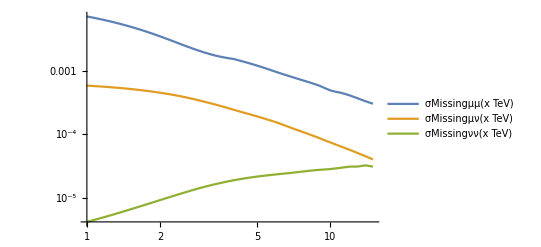

```mathematica
LogLogPlot[{σMissingμμ[x TeV],σMissingμν[x TeV],σMissingνν[x TeV]},{x,1,15},PlotLegends->"Expressions"]
```

## B Anomaly Overlays and Projections

### Plot Styles

```mathematica
(*MyFont="Times";
MyLabelSize=20;
MyTickSize=16;
MyLegendSize=12;
MyOptions=Sequence[
AspectRatio->1,
(*Axes->None,*)
Frame->True,
GridLinesStyle->Lighter[Lighter[Gray]],
LabelStyle->Directive[FontFamily->MyFont,FontSize->MyLabelSize],
FrameStyle->Directive[FontFamily->MyFont,FontSize->MyLabelSize],
FrameTicksStyle->Directive[FontFamily->MyFont,FontSize->MyTickSize],
ImageSize->450];*)
```

### B anomaly fit (from 2103.13370)

```mathematica
(*benchmarkpoint=ListPlot[{{C9bench,C10bench}},PlotMarkers->{"▲",20},PlotStyle->Directive[Darker@Gray]];

C9mean=-0.83;deltaC9=0.23;
C10mean=0.17;deltaC10=0.15;
C9pmean=-0.08;deltaC9p=0.30;
C10pmean=-0.33;deltaC10p=0.19;

rho={{1,0.66,0.38,0.58},{0.66,1,0.54,0.55},{0.38,0.54,1,0.81},{0.58,0.55,0.81,1}};

Cmean={C9mean,C10mean,C9pmean,C10pmean};
deltaC={deltaC9,deltaC10,deltaC9p,deltaC10p};

Cov=Table[0,{ii,4},{jj,4}];
For[ii=1,ii<5,ii++,
For[jj=1,jj<5,jj++,
Cov[[ii,jj]]=rho[[ii,jj]]*deltaC[[ii]]*deltaC[[jj]];
]]
*)
```

```mathematica
(*chi2Fit[C9_,C10_]:=(Cmean-{C9,C10,0,0}).Inverse[Cov].(Cmean-{C9,C10,0,0});
minFit=NMinimize[chi2Fit[C9,C10],{C9,C10}][[1]];*)
```

```mathematica
(*cplot1=ContourPlot[(chi2Fit[C9,C10]-minFit)==2.3,{C9,-1.5,0},{C10,-0.5,1},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]];
cplot2=ContourPlot[(chi2Fit[C9,C10]-minFit)==6,{C9,-1.5,0},{C10,-0.5,1},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]];

elipseFit=Show[cplot1,cplot2,benchmarkpoint,Evaluate[MyOptions],PlotRange->{{-2,1},{-1,2}},Axes->True,AxesOrigin->{0,0},FrameLabel->{"C_9^bsμμ","C_10^bsμμ","global fit from 2103.13370"},
ImageSize->500];*)
```

### B anomaly fit taking into account only clean observables and projection to HL-LHC era

```mathematica
(*(* experimental numbers as of Feb 2022 *)
RKexp=0.846;δpRKexp=Sqrt[0.042^2+0.013^2];δmRKexp=Sqrt[0.039^2+0.012^2];
RKstarexp=0.69;δpRKstarexp=Sqrt[0.11^2+0.05^2];δmRKstarexp=Sqrt[0.07^2+0.05^2];
RKstarlowexp=0.66;δpRKstarlowexp=Sqrt[0.11^2+0.03^2];δmRKstarlowexp=Sqrt[0.07^2+0.03^2];
Bsmumuexp=2.93*10^-9;δBsmumuexp=0.35*10^-9;

(* SM numbers from flavio *)
RKflavio=1.00012634545801;
RKstarflavio=0.99645889107953;
RKstarlowflavio=0.94285030715727;
Bsmumuflavio=3.59758917050452*10^-9;
δBsmumuflavio=0.180036095988949*10^-9;
*)
```

```mathematica
(*(* numerical expressions for the observables (fitted to flavio) *)
RK[C9mu_,C10mu_,C9pmu_,C10pmu_,C9e_,C10e_,C9pe_,C10pe_]:=Module[
{a9mu,a9Remu,a10mu,a10Remu,a9e,a9Ree,a10e,a10Ree,result},
(* coefficients from flavio *)
a9mu=0.030560347148496557;a9Remu=0.23817526529271332;a10mu=0.0305586935585928;a10Remu=-0.2560885165185609;
a9e=0.030567424359061835;a9Ree=0.23823033099747976;a10e=0.030552582457677117;a10Ree=-0.2560373415484727;
result=RKflavio*(1+a9mu*Abs[C9mu+C9pmu]^2+a10mu*Abs[C10mu+C10pmu]^2+a9Remu*Re[C9mu+C9pmu]+a10Remu*Re[C10mu+C10pmu])/(1+a9e*Abs[C9e+C9pe]^2+a10e*Abs[C10e+C10pe]^2+a9Ree*Re[C9e+C9pe]+a10Ree*Re[C10e+C10pe]);
Return[result];]


RKstar[C9mu_,C10mu_,C9pmu_,C10pmu_,C9e_,C10e_,C9pe_,C10pe_]:=Module[
{a9mu,a9Remu,a9Immu,a10mu,a10Remu,a9pmu,a9pRemu,a9pImmu,a10pmu,a10pRemu,a99pRemu,a910pRemu,a1010pRemu,a9e,a9Ree,a9Ime,a10e,a10Ree,a9pe,a9pRee,a9pIme,a10pe,a10pRee,a99pRee,a910pRee,a1010pRee,result},
(* coefficients from flavio *)
a9mu=0.035308267889747384;a9Remu=0.1856699913011867;a9Immu=0.0009358033318459196;a10mu=0.03509501511691309;a10Remu=-0.2940718800871292;
a9pmu=0.03530826788974711;a9pRemu=-0.18963650736835294;a9pImmu=-0.00022774775161533737;a10pmu=0.03509501511691309;a10pRemu=0.21827241029470376;
a99pRemu=-0.052196102728995754;a910pRemu=-0.0011415254488869576;a1010pRemu=-0.05212642507333299;
a9e=0.03518683855267832;a9Ree=0.18503041565793138;a9Ime=0.000932582389028665;a10e=0.03516974874846674;a10Ree=-0.2946977193506965;
a9pe=0.03518683855267832;a9pRee=-0.18898598427931676;a9pIme=-0.00022695499914517385;a10pe=0.03516974874846674;a10pRee=0.2177089190546434;
a99pRee=-0.05201709998687945;a910pRee=-0.0011430343383172243;a1010pRee=-0.05199184169920605;
result=RKstarflavio*(1+a9mu*Abs[C9mu]^2+a10mu*Abs[C10mu]^2+a9pmu*Abs[C9pmu]^2+a10pmu*Abs[C10pmu]^2+a9Remu*Re[C9mu]+a10Remu*Re[C10mu]+a9pRemu*Re[C9pmu]+a10pRemu*Re[C10pmu]+a9Immu*Im[C9mu]+a9pImmu*Im[C9pmu]+a99pRemu*(Re[C9mu]*Re[C9pmu]+Im[C9mu]*Im[C9pmu])+a910pRemu*(Re[C9mu]*Re[C10pmu]+Im[C9mu]*Im[C10pmu])+a1010pRemu*(Re[C10mu]*Re[C10pmu]+Im[C10mu]*Im[C10pmu]))/(1+a9e*Abs[C9e]^2+a10e*Abs[C10e]^2+a9pe*Abs[C9pe]^2+a10pe*Abs[C10pe]^2+a9Ree*Re[C9e]+a10Ree*Re[C10e]+a9pRee*Re[C9pe]+a10pRee*Re[C10pe]+a9Ime*Im[C9e]+a9pIme*Im[C9pe]+a99pRee*(Re[C9e]*Re[C9pe]+Im[C9e]*Im[C9pe])+a910pRee*(Re[C9e]*Re[C10pe]+Im[C9e]*Im[C10pe])+a1010pRee*(Re[C10e]*Re[C10pe]+Im[C10e]*Im[C10pe]));
Return[result];]


RKstarlow[C9mu_,C10mu_,C9pmu_,C10pmu_,C9e_,C10e_,C9pe_,C10pe_]:=Module[
{a9mu,a9Remu,a9Immu,a10mu,a10Remu,a9pmu,a9pRemu,a10pmu,a10pRemu,a99pRemu,a910pRemu,a1010pRemu,a9e,a9Ree,a9Ime,a10e,a10Ree,a9pe,a9pRee,a10pe,a10pRee,a99pRee,a1010pRee,result},
(* coefficients from flavio *)
a9mu=0.010914781267805276;a9Remu=0.045072009375720985;a9Immu=0.00023204386390553416;a10mu=0.010835291467222638;a10Remu=-0.09078776333750876;
a9pmu=0.010914781267805504;a9pRemu=-0.07517216804477166;a10pmu=0.010835291467222523;a10pRemu=0.08599272541652106;
a99pRemu=-0.020555772767158406;a910pRemu=0.002199863911994263;a1010pRemu=-0.020536274392664488;
a9e=0.010484682635023768;a9Ree=0.04321761984929434;a9Ime=0.00022364028125725774;a10e=0.01047958995960454;a10Ree=-0.08780724154271033;
a9pe=0.010484682635023555;a9pRee=-0.07224086326719448;a10pe=0.010479589959604326;a10pRee=0.08271364907702505;a99pRee=-0.01976277529922954;a1010pRee=-0.01975317912690163;
result=RKstarlowflavio*(1+a9mu*Abs[C9mu]^2+a10mu*Abs[C10mu]^2+a9pmu*Abs[C9pmu]^2+a10pmu*Abs[C10pmu]^2+a9Remu*Re[C9mu]+a10Remu*Re[C10mu]+a9pRemu*Re[C9pmu]+a10pRemu*Re[C10pmu]+a9Immu*Im[C9mu]+a99pRemu*(Re[C9mu]*Re[C9pmu]+Im[C9mu]*Im[C9pmu])+a910pRemu*(Re[C9mu]*Re[C10pmu]+Im[C9mu]*Im[C10pmu])+a1010pRemu*(Re[C10mu]*Re[C10pmu]+Im[C10mu]*Im[C10pmu]))/(1+a9e*Abs[C9e]^2+a10e*Abs[C10e]^2+a9pe*Abs[C9pe]^2+a10pe*Abs[C10pe]^2+a9Ree*Re[C9e]+a10Ree*Re[C10e]+a9pRee*Re[C9pe]+a10pRee*Re[C10pe]+a9Ime*Im[C9e]+a99pRee*(Re[C9e]*Re[C9pe]+Im[C9e]*Im[C9pe])+a1010pRee*(Re[C10e]*Re[C10pe]+Im[C10e]*Im[C10pe]));
Return[result];]


BRBsmumu[C10mu_,CSmu_,CPmu_,C10pmu_,CSpmu_,CPpmu_]:=Bsmumuflavio*(Abs[1-1/4.2*(C10mu-C10pmu)-1/4.2*5.3669/0.10566/2*(CPmu-CPpmu)]^2+Abs[1/4.2*5.3669/0.10566/2*(CSmu-CSpmu)]^2)

*)
```

```mathematica
(*(* future experimental uncertainties and benchmark central values *)
(* [note that I added the SM uncertainties in the LFU ratios] *)
BsmumuexpFUTURE=BRBsmumu[C10bench,0,0,0,0,0];δBsmumuexpFUTURE=0.16*10^-9;
RKexpFUTURE=RK[C9bench,C10bench,0,0,0,0,0,0];δRKexpFUTURE=Sqrt[0.007^2+0.01^2];
RKstarexpFUTURE=RKstar[C9bench,C10bench,0,0,0,0,0,0];δRKstarexpFUTURE=Sqrt[0.008^2+0.01^2];
RKstarlowexpFUTURE=RKstarlow[C9bench,C10bench,0,0,0,0,0,0];δRKstarlowexpFUTURE=Sqrt[0.008^2+0.03^2];
*)
```

```mathematica
(*(* define chi2 functions *)

LFUchi2[C9mu_,C10mu_]:=If[RK[C9mu,C10mu,0,0,0,0,0,0]<RKexp,(RK[C9mu,C10mu,0,0,0,0,0,0]-RKexp)^2/δmRKexp^2,(RK[C9mu,C10mu,0,0,0,0,0,0]-RKexp)^2/δpRKexp^2]+If[RKstar[C9mu,C10mu,0,0,0,0,0,0]<RKstarexp,(RKstar[C9mu,C10mu,0,0,0,0,0,0]-RKstarexp)^2/δmRKstarexp^2,(RKstar[C9mu,C10mu,0,0,0,0,0,0]-RKstarexp)^2/δpRKstarexp^2]+If[RKstarlow[C9mu,C10mu,0,0,0,0,0,0]<RKstarlowexp,(RKstarlow[C9mu,C10mu,0,0,0,0,0,0]-RKstarlowexp)^2/δmRKstarlowexp^2,(RKstarlow[C9mu,C10mu,0,0,0,0,0,0]-RKstarlowexp)^2/δpRKstarlowexp^2]
chi2[C9mu_,C10mu_]:=LFUchi2[C9mu,C10mu]+(BRBsmumu[C10mu,0,0,0,0,0]-Bsmumuexp)^2/δBsmumuexp^2
min=NMinimize[chi2[C9,C10],{C9,C10}][[1]];

LFUchi2FUTURE[C9mu_,C10mu_]:=(RK[C9mu,C10mu,0,0,0,0,0,0]-RKexpFUTURE)^2/δRKexpFUTURE^2+(RKstar[C9mu,C10mu,0,0,0,0,0,0]-RKstarexpFUTURE)^2/δRKstarexpFUTURE^2+(RKstarlow[C9mu,C10mu,0,0,0,0,0,0]-RKstarlowexpFUTURE)^2/δRKstarlowexpFUTURE^2;
chi2FUTURE[C9mu_,C10mu_]:=LFUchi2FUTURE[C9mu,C10mu]+(BRBsmumu[C10mu,0,0,0,0,0]-BsmumuexpFUTURE)^2/δBsmumuexpFUTURE^2
minFUTURE=NMinimize[chi2FUTURE[C9,C10],{C9,C10}][[1]];
*)
```

```mathematica
(*cplot3=ContourPlot[(chi2[C9,C10]-min)==2.3,{C9,-1.5,0.7},{C10,-1,1.5},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]];
cplot4=ContourPlot[(chi2[C9,C10]-min)==6,{C9,-1.5,0.7},{C10,-0.5,1.5},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]];

elipse=Show[cplot4,cplot3,benchmarkpoint,Evaluate[MyOptions],PlotRange->{{-2,1},{-1,2}},Axes->True,AxesOrigin->{0,0},FrameLabel->{"C_9^bsμμ","C_10^bsμμ","fit to clean observables, 2022"},
ImageSize->500];*)
```

```mathematica
(*cplot5=ContourPlot[(chi2FUTURE[C9,C10]-minFUTURE)==2.3,{C9,-1,0},{C10,0,1},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]];
cplot6=ContourPlot[(chi2FUTURE[C9,C10]-minFUTURE)==6,{C9,-1,0},{C10,0,1},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]];

elipseFUTURE=Show[cplot6,cplot5,benchmarkpoint,Evaluate[MyOptions],PlotRange->{{-2,1},{-1,2}},Axes->True,AxesOrigin->{0,0},FrameLabel->{"C_9^bsμμ","C_10^bsμμ","fit to clean observables, HL-LHC"},
ImageSize->500];*)
```

### Plots

```mathematica
(*elipse
elipseFUTURE*)
```

### Plot Styles

```mathematica
<<FixPolygons.m
```

```mathematica
(* colors for mathematica *)
MyDarkOrange=RGBColor[255/255,127/255,14/255];
MyOrange=RGBColor[255/255,191/255,135/255];
MyDarkRed=RGBColor[214/255,39/255,40/255];
MyRed=RGBColor[236/255,146/255,147/255];
MyDarkBlue=RGBColor[31/255,119/255,180/255];
MyBlue=RGBColor[127/255,190/255,233/255];
MyDarkYellow=RGBColor[188/255,189/255,34/255];
MyYellow=RGBColor[233/255,234/255,133/255];
MyDarkGreen=RGBColor[45/255,160/255,45/255];
MyGreen=RGBColor[135/255,222/255,135/255];
MyDarkPink=RGBColor[227/255,120/255,194/255];
MyPink=RGBColor[241/255,187/255,225/255];
MyDarkPurple=RGBColor[148/255,103/255,189/255];
MyPurple=RGBColor[202/255,179/255,222/255];

(* colors for MaTeX *)
MyMaTeXcolors={
"\\definecolor{MyDarkOrange}{rgb}"<>ToString[MyDarkOrange/.RGBColor[x__]->{x}//N],
"\\definecolor{MyOrange}{rgb}"<>ToString[MyOrange/.RGBColor[x__]->{x}//N],
"\\definecolor{MyDarkRed}{rgb}"<>ToString[MyDarkRed/.RGBColor[x__]->{x}//N],
"\\definecolor{MyRed}{rgb}"<>ToString[MyRed/.RGBColor[x__]->{x}//N],
"\\definecolor{MyDarkBlue}{rgb}"<>ToString[MyDarkBlue/.RGBColor[x__]->{x}//N],
"\\definecolor{MyBlue}{rgb}"<>ToString[MyBlue/.RGBColor[x__]->{x}//N],
"\\definecolor{MyDarkYellow}{rgb}"<>ToString[MyDarkYellow/.RGBColor[x__]->{x}//N],
"\\definecolor{MyYellow}{rgb}"<>ToString[MyYellow/.RGBColor[x__]->{x}//N],
"\\definecolor{MyDarkGreen}{rgb}"<>ToString[MyDarkGreen/.RGBColor[x__]->{x}//N],
"\\definecolor{MyGreen}{rgb}"<>ToString[MyGreen/.RGBColor[x__]->{x}//N],
"\\definecolor{MyDarkPink}{rgb}"<>ToString[MyDarkPink/.RGBColor[x__]->{x}//N],
"\\definecolor{MyPink}{rgb}"<>ToString[MyPink/.RGBColor[x__]->{x}//N],
"\\definecolor{MyDarkPurple}{rgb}"<>ToString[MyDarkPurple/.RGBColor[x__]->{x}//N],
"\\definecolor{MyPurple}{rgb}"<>ToString[MyPurple/.RGBColor[x__]->{x}//N]};
```

```mathematica
SetOptions[MaTeX,FontSize->16,"Preamble"->Join[{"\\usepackage{amsmath,amssymb,slashed}","\\usepackage{xcolor,txfonts}"},MyMaTeXcolors]];
```

```mathematica
MyFont="Latin Modern Roman";
MyLabelSize=36;
MyTickSize=16;
MyLegendSize=12;
```

```mathematica
MyOptions=Sequence[
AspectRatio->1,
(*Axes->None,*)
{Frame->True,FrameStyle->Directive[Medium,Black]},
PlotRangePadding->None,
GridLinesStyle->Lighter[Lighter[Gray]],
(*BaseStyle-> Directive[Black,FontFamily->MyFont,FontSize-> MyLabelSize],*)
LabelStyle->Directive[Black,FontFamily->MyFont,FontSize->MyLabelSize],
FrameStyle->Directive[Black,FontFamily->MyFont,FontSize->MyLabelSize],
FrameTicksStyle->Directive[Black,FontFamily->MyFont,FontSize->MyTickSize]];
```

```mathematica
(*Bare bones tickmaker*)
tickmaker[i_,string_,mag_,L_,tt_]:={i,MaTeX[string,Magnification->mag],{L,0},Directive[Black,Thickness->tt]}
UnlabeledTick[i_,L_,tt_]:={Log10[10^i],"",{L,0},Directive[Black,Thickness->tt]}

(*LOG TICKS*)
LabeledLogTick[i_,mag_,L_,tt_]:=Which[
	i==0,tickmaker[i,"1",mag,L,tt],
	i==1,tickmaker[i,"10",mag,L,tt],
	i≠ 0&&i≠ 1,tickmaker[i,"10^{"<>ToString[Round[i,1]]<>"}",mag,L,tt]]

(*Functions needed to compute the tick list*)
MakeList$short[min_,max_]:=Cases[Flatten@Table[Table[10^x y,{y,1,9}],{x,Floor[min],Ceiling[max]}]//N,x_/;10^max≥ x≥10^min ]
MakeList$long[min_,max_]:=Cases[Table[10^xx,{xx,Floor@min,Ceiling@max}]//N,x_/;10^max≥ x≥10^min ]
MakeList$label[min_,max_,skip_]:=Cases[Table[10^xx,{xx,Floor@min,Ceiling@max,skip}]//N,x_/;10^max≥ x≥10^min ]

logticks[min_,max_,mag_:1,L1_:0.02,L2_:0.01,tt_:0.005,skip:_1]:=Block[{
	ticklabels=LabeledLogTick[#,mag,0,tt]&/@Log10[MakeList$label[min,max,skip]],
	longticks=UnlabeledTick[#,L1,tt]&/@Log10[MakeList$long[min,max]],
	shortticks=UnlabeledTick[#,L2,tt]&/@Log10[MakeList$short[min,max]]},
	Join[ticklabels,longticks,shortticks]]

logticks$nolabel[min_,max_,mag_:1,L1_:0.02,L2_:0.01,tt_:0.005]:=Block[{
	longticks=UnlabeledTick[#,L1,tt]&/@Log10[MakeList$long[min,max]],
	shortticks=UnlabeledTick[#,L2,tt]&/@Log10[MakeList$short[min,max]]},
	Join[longticks,shortticks]]
```

### Updated Rare B Decay Fit

```mathematica
C9mean=-0.80;deltaC9=0.22;
C10mean=0.12;deltaC10=0.20;
rho={{1,-0.30},{-0.30,1}};
benchmarkpoint=ListPlot[{{C9bench,C10bench}},PlotMarkers->{"▲",20},PlotStyle->Directive[Darker@Gray]];

Cmean={C9mean,C10mean};
deltaC={deltaC9,deltaC10};

Cov=Table[0,{ii,2},{jj,2}];
For[ii=1,ii<3,ii++,
For[jj=1,jj<3,jj++,
Cov[[ii,jj]]=rho[[ii,jj]]*deltaC[[ii]]*deltaC[[jj]];
]]
```

```mathematica
chi2Fit[C9_,C10_]:=(Cmean-{C9,C10}).Inverse[Cov].(Cmean-{C9,C10});
minFit=NMinimize[chi2Fit[C9,C10],{C9,C10}][[1]];
```

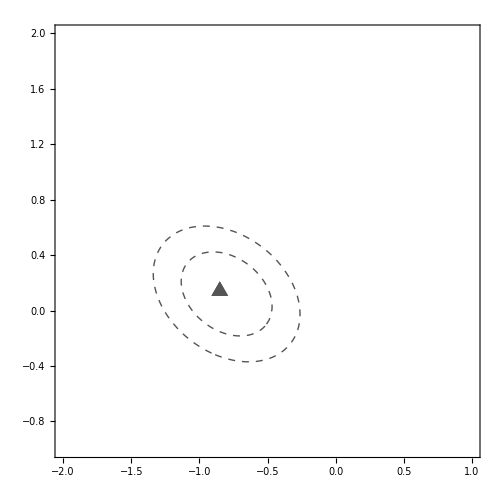

```mathematica
ContourPlot[(chi2Fit[C9,C10]-minFit)==2.3,{C9,-1.5,0},{C10,-0.5,1},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]];
ContourPlot[(chi2Fit[C9,C10]-minFit)==6,{C9,-1.5,0},{C10,-0.5,1},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]];

elipse=Show[%,%%,benchmarkpoint,Evaluate[MyOptions],PlotRange->{{-2,1},{-1,2}},Axes->True,AxesOrigin->{0,0},FrameLabel->(MaTeX[#,Magnification->1.3]&/@{"\\Delta C_9^\\text{univ.}","\\Delta C_{10}^\\text{univ.}","{\\text{rare B decay fit, Winter 2023}}"}),
ImageSize->500]
```

```mathematica
C9meanFuture=-0.80;deltaC9Future=0.2;
C10meanFuture=0.02;deltaC10Future=0.1;
rhoFuture={{1,-0.18},{-0.18,1}};

CmeanFuture={C9meanFuture,C10meanFuture};
deltaCFuture={deltaC9Future,deltaC10Future};

CovFuture=Table[0,{ii,2},{jj,2}];
For[ii=1,ii<3,ii++,
For[jj=1,jj<3,jj++,
CovFuture[[ii,jj]]=rhoFuture[[ii,jj]]*deltaCFuture[[ii]]*deltaCFuture[[jj]];
]]
```

```mathematica
chi2FitFuture[C9_,C10_]:=(CmeanFuture-{C9,C10}).Inverse[CovFuture].(CmeanFuture-{C9,C10});
minFitFuture=NMinimize[chi2FitFuture[C9,C10],{C9,C10}][[1]];
```

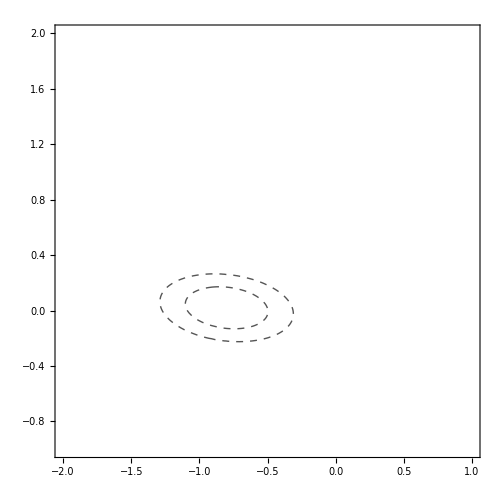

```mathematica
ContourPlot[(chi2FitFuture[C9,C10]-minFitFuture)==2.3,{C9,-1.5,0},{C10,-0.5,1},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]];
ContourPlot[(chi2FitFuture[C9,C10]-minFitFuture)==6,{C9,-1.5,0},{C10,-0.5,1},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]];

elipseFuture=Show[%,%%,Evaluate[MyOptions],PlotRange->{{-2,1},{-1,2}},Axes->True,AxesOrigin->{0,0},FrameLabel->(MaTeX[#,Magnification->1.3]&/@{"\\Delta C_9^\\text{univ.}","\\Delta C_{10}^\\text{univ.}","{\\text{rare B decay fit, 2040}}"}),
ImageSize->500]
```

### Plots

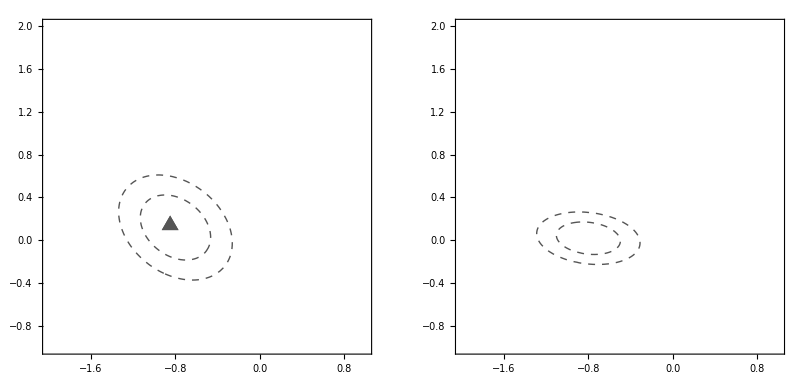

```mathematica
GraphicsGrid[{{elipse,elipseFuture}}]
```

## 2D Coefficient Space Contour plots

### Plotting Functions

```mathematica
Clear@plotterBenchHLLHC
jointcolour=Red;
plotpoints=60;
plotterBenchHLLHC[PAFB_:0,Pσ_:0,eCM_:10TeV,lumi_:10defaultLumi(*10/ab*),c_:0.7]:=Show[ContourPlot[AFBdiscrepancyBench[eCM,-PAFB,PAFB,lumi,c,x,y]/δAFB[eCM,-PAFB,PAFB,lumi,c,C9collider@eCM,C10collider@eCM],{x,minC9,maxC9},{y,minC10,maxC10},Contours->{ 1,2},FrameLabel->{"C_9"//MaTeX,"C_{10}"//MaTeX},PlotPoints->plotpoints,ContourShading->{Opacity[0.3,Blue],Opacity[0.15,Blue],None},ContourStyle->Directive[Opacity[1,Black]](*,FrameTicks->None*),PlotRangePadding->0,Axes->True],ContourPlot[NdiscrepancyBench[eCM,-Pσ,Pσ,x,y,lumi]/errorNevents[eCM,-Pσ,Pσ,C9collider@eCM,C10collider@eCM,lumi],{x,minC9,maxC9},{y,minC10,maxC10},Contours->{ 1,2},FrameLabel->{"C_9"//MaTeX,"C_{10}"//MaTeX},PlotPoints->plotpoints,ContourShading->{Opacity[0.3,Green],Opacity[0.15,Green],None},ContourStyle->Directive[Opacity[1,Black]](*,FrameTicks->None*),PlotRangePadding->0,Axes->True],ContourPlot[combinedErrOverestimate[eCM,-PAFB,PAFB,-Pσ,Pσ,x,y,lumi,c],{x,minC9,maxC9},{y,minC10,maxC10},Contours->{ Sqrt[2.3],Sqrt[6] },FrameLabel->{"C_9"//MaTeX,"C_{10}"//MaTeX},PlotPoints->plotpoints,ContourShading->{jointcolour,Opacity[0.8,jointcolour],None},ContourStyle->Directive[Opacity[1,Black]](*,FrameTicks->None*),PlotRangePadding->0,Axes->True],ContourPlot[(chi2FitFuture[x,y]-minFitFuture)==2.3,{x,minC9,maxC9},{y,minC10,maxC10},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]],ContourPlot[(chi2FitFuture[x,y]-minFitFuture)==6,{x,minC9,maxC9},{y,minC10,maxC10},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]]]//FixPolygons
```

```mathematica
Clear@plotterBenchCurrent
plotterBenchCurrent[PAFB_:0,Pσ_:0,eCM_:10TeV,lumi_:defaultLumi(*1/ab for present*),c_:0.7]:=Show[ContourPlot[AFBdiscrepancyBench[eCM,-PAFB,PAFB,lumi,c,x,y]/δAFB[eCM,-PAFB,PAFB,lumi,c,C9collider@eCM,C10collider@eCM],{x,minC9,maxC9},{y,minC10,maxC10},Contours->{ 1,2},FrameLabel->{"C_9"//MaTeX,"C_{10}"//MaTeX},PlotPoints->plotpoints,ContourShading->{Opacity[0.3,Blue],Opacity[0.15,Blue],None},ContourStyle->Directive[Opacity[1,Black]](*,FrameTicks->None*),PlotRangePadding->0,Axes->True],ContourPlot[NdiscrepancyBench[eCM,-Pσ,Pσ,x,y,lumi]/errorNevents[eCM,-Pσ,Pσ,C9collider@eCM,C10collider@eCM,lumi],{x,minC9,maxC9},{y,minC10,maxC10},Contours->{ 1,2},FrameLabel->{"C_9"//MaTeX,"C_{10}"//MaTeX},PlotPoints->plotpoints,ContourShading->{Opacity[0.3,Green],Opacity[0.15,Green],None},ContourStyle->Directive[Opacity[1,Black]](*,FrameTicks->None*),PlotRangePadding->0,Axes->True],ContourPlot[combinedErrOverestimate[eCM,-PAFB,PAFB,-Pσ,Pσ,x,y,lumi,c],{x,minC9,maxC9},{y,minC10,maxC10},Contours->{ Sqrt[2.3],Sqrt[6] },FrameLabel->{"C_9"//MaTeX,"C_{10}"//MaTeX},PlotPoints->plotpoints,ContourShading->{jointcolour,Opacity[0.8,jointcolour],None},ContourStyle->Directive[Opacity[1,Black]](*,FrameTicks->None*),PlotRangePadding->0,Axes->True],ContourPlot[(chi2Fit[x,y]-minFit)==2.3,{x,minC9,maxC9},{y,minC10,maxC10},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]],ContourPlot[(chi2Fit[x,y]-minFit)==6,{x,minC9,maxC9},{y,minC10,maxC10},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]]]//FixPolygons
```

```mathematica
testPlotpoints=60;
Clear@plotterPolarizationOverlayCurrent
plotterPolarizationOverlayCurrent[PAFB_:0.5,Pσ_:0.5,eCM_:10TeV,lumi_:defaultLumi]:=Show[ContourPlot[AFBdiscrepancyBench[eCM,-PAFB,PAFB,lumi,0.7,x,y]/δAFB[eCM,-PAFB,PAFB,lumi,0.7,C9collider@eCM,C10collider@eCM],{x,minC9,maxC9},{y,minC10,maxC10},Contours->{ 1,2},FrameLabel->{"C_9"//MaTeX,"C_{10}"//MaTeX},PlotPoints->testPlotpoints,ContourShading->{Opacity[0.3,Blue],Opacity[0.15,Blue],None},ContourStyle->Directive[Opacity[1,Black]](*,FrameTicks->None*),PlotRangePadding->0,Axes->True],ContourPlot[NdiscrepancyBench[eCM,-Pσ,Pσ,x,y,lumi]/errorNevents[eCM,-Pσ,Pσ,C9collider@eCM,C10collider@eCM,lumi],{x,minC9,maxC9},{y,minC10,maxC10},Contours->{ 1,2},FrameLabel->{"C_9"//MaTeX,"C_{10}"//MaTeX},PlotPoints->testPlotpoints,ContourShading->{Opacity[0.3,Green],Opacity[0.15,Green],None},ContourStyle->Directive[Opacity[1,Black]](*,FrameTicks->None*),PlotRangePadding->0,Axes->True],ContourPlot[combinedErrOverestimate[eCM,-PAFB,PAFB,-Pσ,Pσ,x,y,lumi],{x,minC9,maxC9},{y,minC10,maxC10},Contours->{ Sqrt[2.3],Sqrt[6] },FrameLabel->{"C_9"//MaTeX,"C_{10}"//MaTeX},PlotPoints->testPlotpoints,ContourShading->{jointcolour,Opacity[0.8,jointcolour],None},ContourStyle->Directive[Opacity[1,Black]](*,FrameTicks->None*),PlotRangePadding->0,Axes->True],ContourPlot[combinedErrOverestimate[eCM,0,0,0,0,x,y,lumi],{x,minC9,maxC9},{y,minC10,maxC10},Contours->{ Sqrt[2.3],Sqrt[6] },FrameLabel->{"C_9"//MaTeX,"C_{10}"//MaTeX},PlotPoints->testPlotpoints,ContourShading->{jointcolour,Opacity[0.8,jointcolour],None},ContourStyle->Directive[Opacity[1,Black]](*,FrameTicks->None*),PlotRangePadding->0,Axes->True],ContourPlot[(chi2Fit[x,y]-minFit)==2.3,{x,minC9,maxC9},{y,minC10,maxC10},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]],ContourPlot[(chi2Fit[x,y]-minFit)==6,{x,minC9,maxC9},{y,minC10,maxC10},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]]]//FixPolygons
(*Same as polarized current, but overlays the unpolarized contours for the joint χ^2*)
Clear@plotterPolarizationOverlayHLLHC
plotterPolarizationOverlayHLLHC[PAFB_:0.5,Pσ_:0.5,eCM_:10TeV,lumi_:10defaultLumi(*10/ab*)]:=Show[ContourPlot[AFBdiscrepancyBench[eCM,-PAFB,PAFB,lumi,0.7,x,y]/δAFB[eCM,-PAFB,PAFB,lumi,0.7,C9collider@eCM,C10collider@eCM],{x,minC9,maxC9},{y,minC10,maxC10},Contours->{ 1,2},FrameLabel->{"C_9"//MaTeX,"C_{10}"//MaTeX},PlotPoints->testPlotpoints,ContourShading->{Opacity[0.3,Blue],Opacity[0.15,Blue],None},ContourStyle->Directive[Opacity[1,Black]](*,FrameTicks->None*),PlotRangePadding->0,Axes->True],ContourPlot[NdiscrepancyBench[eCM,-Pσ,Pσ,x,y,lumi]/errorNevents[eCM,-Pσ,Pσ,C9collider@eCM,C10collider@eCM,lumi],{x,minC9,maxC9},{y,minC10,maxC10},Contours->{ 1,2},FrameLabel->{"C_9"//MaTeX,"C_{10}"//MaTeX},PlotPoints->testPlotpoints,ContourShading->{Opacity[0.3,Green],Opacity[0.15,Green],None},ContourStyle->Directive[Opacity[1,Black]](*,FrameTicks->None*),PlotRangePadding->0,Axes->True],ContourPlot[combinedErrOverestimate[eCM,-PAFB,PAFB,-Pσ,Pσ,x,y,lumi],{x,minC9,maxC9},{y,minC10,maxC10},Contours->{ Sqrt[2.3],Sqrt[6] },FrameLabel->{"C_9"//MaTeX,"C_{10}"//MaTeX},PlotPoints->testPlotpoints,ContourShading->{jointcolour,Opacity[0.8,jointcolour],None},ContourStyle->Directive[Opacity[1,Black]](*,FrameTicks->None*),PlotRangePadding->0,Axes->True],ContourPlot[combinedErrOverestimate[eCM,0,0,0,0,x,y,lumi],{x,minC9,maxC9},{y,minC10,maxC10},Contours->{ Sqrt[2.3],Sqrt[6] },FrameLabel->{"C_9"//MaTeX,"C_{10}"//MaTeX},PlotPoints->testPlotpoints,ContourShading->{jointcolour,Opacity[0.8,jointcolour],None},ContourStyle->Directive[Opacity[1,Black]](*,FrameTicks->None*),PlotRangePadding->0,Axes->True],ContourPlot[(chi2FitFuture[x,y]-minFitFuture)==2.3,{x,minC9,maxC9},{y,minC10,maxC10},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]],ContourPlot[(chi2FitFuture[x,y]-minFitFuture)==6,{x,minC9,maxC9},{y,minC10,maxC10},ContourShading->None,ContourStyle->Directive[Darker@Gray,Thick,Dashed]]]//FixPolygons
```

### Plots

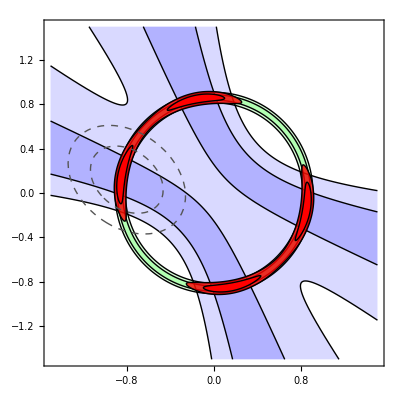

```mathematica
plotterBenchCurrent[0,0,10TeV,defaultLumi,0.6]
```

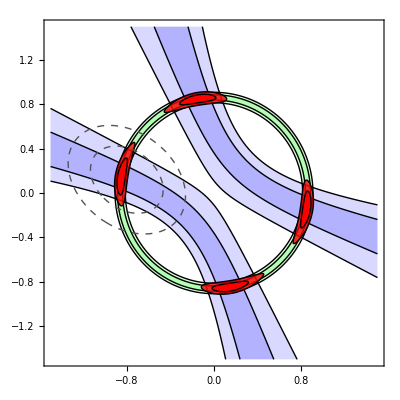

```mathematica
plotterBenchCurrent[0,0,10TeV,defaultLumi,0.65]
```

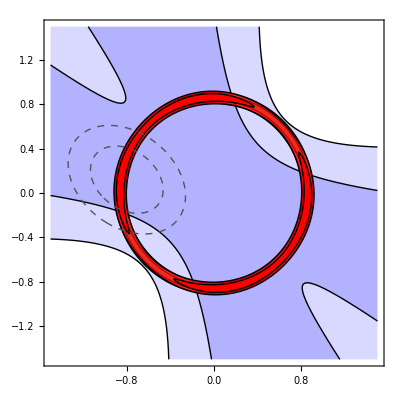

```mathematica
plotterBenchCurrent[0,0,10TeV,defaultLumi,0.55]
```

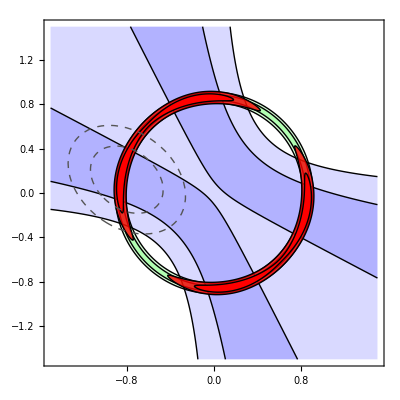

```mathematica
plotterBenchCurrent[0,0,10TeV,defaultLumi,0.575]
```

```mathematica
UnpolarizedPlotCurrent=plotterBenchCurrent[]
```

```mathematica
UnpolarizedPlotHLLHC=plotterBenchHLLHC[]
```

```mathematica
PolarizedPlotCurrent=plotterBenchCurrent[0.5,0.5]
```

```mathematica
PolarizedPlotHLLHC=plotterBenchHLLHC[0.5,0.5]
```

```mathematica
CurrentComplementarity=Show[UnpolarizedPlotCurrent,PolarizedPlotCurrent]
```

```mathematica
HLLHCComplementarity=Show[UnpolarizedPlotHLLHC,PolarizedPlotHLLHC]
```

```mathematica
RedZoneComplementarityCurrent=plotterPolarizationOverlayCurrent[]
```

```mathematica
RedZoneComplementarityHLLHC=plotterPolarizationOverlayHLLHC[]
```

## NP Test Scale Histograms

```mathematica
histoWithCS=BarChart[{{49,114,76,86},{61,128,76,86},{51,115,76,86},{59,125,76,86},{411,614,70,82}},AxesLabel->MaTeX/@{"","\\Lambda/\\text{TeV}"},ChartLabels->{MaTeX[{"C_9","C_{10}","C_9'","C_{10}'","C_{S}^{(')}"}],None},ChartLegends->{"Rare B decays: Current","Rare B decays: High Lumi","10 TeV Muon Collider: 1 ab^-1","10 TeV Muon Collider: 10 ab^-1"}]
histoVector=BarChart[{{49,114,76,86},{61,128,76,86},{51,115,76,86},{59,125,76,86}},AxesLabel->MaTeX[{"","\\Lambda/\\text{TeV}"}],ChartLabels->{MaTeX[{"C_9","C_{10}","C_9'","C_{10}'"}],None},ChartLegends->{"Rare B decays: Current","Rare B decays: High Lumi","10 TeV Muon Collider: 1 ab^-1","10 TeV Muon Collider: 10 ab^-1"}]
histoScalar=BarChart[{{411,614,70,82}},AxesLabel->MaTeX[{"","\\Lambda/\\text{TeV}"}],ChartLabels->{{MaTeX["C_{S}^{(')}"]},None},ChartLegends->{"(1) Rare B decays: Current","(2) Rare B decays: High Lumi","(3) 10 TeV Muon Collider: 1 ab^-1","(4) 10 TeV Muon Collider: 10 ab^-1"}(*,ChartStyle->{Red, Green, Blue, Cyan}*)]
```

-Graphics-

-Graphics-

-Graphics-

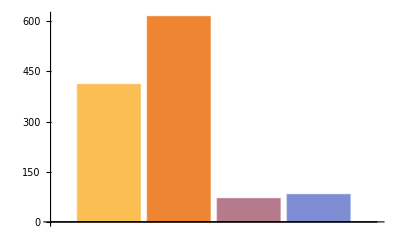

```mathematica
testChart=BarChart[{{411,614,70,82}}]
```

```mathematica
cols=DominantColors[testChart]
```

{RGBColor[6.636694485562685*^-8, 6.636686583450336*^-8, 6.636681958909097*^-8, 0.],RGBColor[0.929412641068735, 0.5215671776876725, 0.1999999806245356, 1.],RGBColor[0.9843145964388565, 0.7450970426818757, 0.32548989099572406, 1.],RGBColor[0.498038503802027, 0.5568623697026656, 0.831371613400468, 1.],RGBColor[0.7098042481322416, 0.4823520062366196, 0.5490188843403645, 1.],RGBColor[0.3999997979338314, 0.3999994754160956, 0.39999930595934846, 1.]}

```mathematica
colors={cols[[3]],cols[[2]],cols[[5]],cols[[4]]}
colorswithBlend=Append[colors,{Blend[{colors[[1]],colors[[3]]}],Blend[{colors[[2]],colors[[4]]}]}]//Flatten
```

{RGBColor[0.9843145964388565, 0.7450970426818757, 0.32548989099572406, 1.],RGBColor[0.929412641068735, 0.5215671776876725, 0.1999999806245356, 1.],RGBColor[0.7098042481322416, 0.4823520062366196, 0.5490188843403645, 1.],RGBColor[0.498038503802027, 0.5568623697026656, 0.831371613400468, 1.]}

{RGBColor[0.9843145964388565, 0.7450970426818757, 0.32548989099572406, 1.],RGBColor[0.929412641068735, 0.5215671776876725, 0.1999999806245356, 1.],RGBColor[0.7098042481322416, 0.4823520062366196, 0.5490188843403645, 1.],RGBColor[0.498038503802027, 0.5568623697026656, 0.831371613400468, 1.],RGBColor[0.8470594222855491, 0.6137245244592476, 0.43725438766804425, 1.],RGBColor[0.713725572435381, 0.539214773695169, 0.5156857970125017, 1.]}

```mathematica
histoC9=BarChart[{{ΛbsC9current,ΛbsC9future,Λvec1abMC,Λvec10abMC,ΛjointC9current1ab,ΛjointC9future10ab}},AxesLabel->MaTeX[{"","\\Lambda/\\text{TeV}"}],ChartLabels->{MaTeX[{"C_9",}],None},ChartLegends->{"(1) Rare B decays: Current","(2) Rare B decays: High Lumi","(3) 10 TeV Muon Collider: 1 ab^-1","(4) 10 TeV Muon Collider: 10 ab^-1", "(5) Combined Fit: (1) + (3)","(6) Combined Fit: (2) + (4)"},ChartStyle->colorswithBlend]
```

-Graphics-

```mathematica
(*SetDirectory["C:\\Users\\sadit\\Downloads"];
Export["HistogramOfScales_C9.pdf",histoC9,ImageResolution->600,"AllowRasterization"->False]
Export["HistogramOfScales_C9.png",histoC9,ImageResolution->600,"AllowRasterization"->False]
Export["HistogramOfScales_Scalar.pdf",histoScalar,ImageResolution->600,"AllowRasterization"->False]
Export["HistogramOfScales_Scalar.png",histoScalar,ImageResolution->600,"AllowRasterization"->False]*)
```

```mathematica
Ceiling@(1/√(4(GFermi/(√2))1000^2 Vtb Vts (αEM/(4π))0.40))
```

56

```mathematica
NSolve[chi2Fit[r,0]==4,r]
NSolve[chi2FitFuture[r,0]==4,r]
```

{{r→-1.1608},{r→-0.36}}

{{r→-1.18429},{r→-0.401306}}